# Banco de Dados Escolas de Botucatu

#### TODO List

```mathematica
strtasks="Incluir Legendas para o Modelo pqq
Arrumar descritores dos eixos com problemas
Resolver discrepâncias entre os que responderam e a linha de base.
Calcular a média da idade de iniciação.
Apresentar dados da ambinge
Apresentar dados da familal
Incluir Médias nas comparações
Incluir Número de Participantes no Título das Tabelas
Incluir Descrição Detalhada da Metodologia de Determinação da Classe Social
Usar SortByKey
Gerar Funções para a sessão de Correlação
Resolver Problemas com sa tabelas do LSD";
listasks=StringSplit[strtasks,"\n"];
TextGrid[Table[{Checkbox[],Style[listasks[[i]],14]},{i,1,Length[listasks]}]]
```

```mathematica
{{, Lidar com Missing de Forma Consistente}, {, □}, {, □}, {, □}, {, □}, {, □}, {, □}, {, □}, {, □}, {, Usar SortByKey}, {, □}, {, □}}
```

## Pacotes Externos

```mathematica
Needs["RLink`"]
```

```mathematica
InstallR[]
REvaluate["sample(1:100,10)"]
```

REvaluate::crash: Crash in low-level RLink component or in R runtime. Please reinstall RLink via InstallR

$Failed

## Definições Gerais

Definições Básicas

```mathematica
prefix="/Users/neylemke/Luisa/BancodeDadosDoutorado/"
Import[prefix<>"bbapackage.wl"]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/

Material de Apoio

```mathematica
str="Televisoresemcores 0 1 2 3 4
Videocassete 0 2 2 2 2
Rádios 0 1 2 3 4
Banheiros 0 4 5 6 7
Automóveis 0 4 7 9 9
Empregadasmensalistas 0 3 4 4 4
Máquinaslavar 0 2 2 2 2
Geladeira 0 4 4 4 4
Freezer* 0 2 2 2 2";
```

c

```mathematica
strtable=StringReplace[str,{" "-> " & ","\n"-> "\\\\\n"}]
```

Televisoresemcores & 0 & 1 & 2 & 3 & 4\\
Videocassete & 0 & 2 & 2 & 2 & 2\\
Rádios & 0 & 1 & 2 & 3 & 4\\
Banheiros & 0 & 4 & 5 & 6 & 7\\
Automóveis & 0 & 4 & 7 & 9 & 9\\
Empregadasmensalistas & 0 & 3 & 4 & 4 & 4\\
Máquinaslavar & 0 & 2 & 2 & 2 & 2\\
Geladeira & 0 & 4 & 4 & 4 & 4\\
Freezer* & 0 & 2 & 2 & 2 & 2

```mathematica
tabTex=" \\begin{tabular}{lrrrrr}
        \\toprule"<> 
" & \\multicolumn{5}{c}{Quantidade de Ítens} \\\\\n
\\cmidrule(r){2-6} 
Ítens & 0 & 1 & 2 & 3 & 4+ \\\\\n
\\midrule
Televisores em Cores & 0 & 1 & 2 & 3 & 4\\\\\n
Videocassete & 0 & 2 & 2 & 2 & 2\\\\\n
Rádios & 0 & 1 & 2 & 3 & 4\\\\\n
Banheiros & 0 & 4 & 5 & 6 & 7\\\\\n
Automóveis & 0 & 4 & 7 & 9 & 9\\\\\n
Empregadas Mensalistas & 0 & 3 & 4 & 4 & 4\\\\\n
Máquinas Lavar & 0 & 2 & 2 & 2 & 2\\\\\n
Geladeira & 0 & 4 & 4 & 4 & 4\\\\\n
Freezer & 0 & 2 & 2 & 2 & 2 \\\\
\\bottomrule
\\end{tabular}
";
Export[prefix<>"tabbens.tex",corrigeAcentos[tabTex],"String"];
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabbens.tex

```mathematica
compilaTex[corrigeAcentos[tabTex],prefix]
```

-Graphics-

```mathematica
tabTex=" \\begin{tabular}{lc}
        \\toprule
 Formação Chefe & Peso \\\\\n
\\midrule \\\\
Até 3$ ^a$ Série Fundamental & 0 \\\\\n
4$^a$  Série Fundamental &  1 \\\\ \n
Fundamental completo & 2 \\\\\n
Médio completo & 4 \\\\ \n
Superior completo & 8 \\\\\n
\\bottomrule
\\end{tabular}
";
Export[prefix<>"tabinstrchef.tex",corrigeAcentos[tabTex],"String"]
compilaTex[corrigeAcentos[tabTex],prefix]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabinstrchef.tex

-Graphics-

```mathematica
StringReplace["classeE=Interval[{0,7}];
classeD=Interval[{8,13}];
classeC2=Interval[{14,17}];
classeC1=Interval[{18,22}];
classeB2=Interval[{23,28}];
classeB1=Interval[{29,33}];
classeA2=Interval[{34,41}];
classeA1=Interval[{42,46}];",{"classe"->"","Interval[{"->"", "}]"->"",","->"-",";"->"\\\\n", "="->" & "}]
```

E & 0-7\\n
D & 8-13\\n
C2 & 14-17\\n
C1 & 18-22\\n
B2 & 23-28\\n
B1 & 29-33\\n
A2 & 34-41\\n
A1 & 42-46\\n

```mathematica
tabTex="\\begin{tabular}{lc}
        \\toprule
Classe Intervalo  &  \\\\\n
\\midrule
E & 0-7\\\\
D & 8-13\\\\
C2 & 14-17\\\\
C1 & 18-22\\\\
B2 & 23-28\\\\
B1 & 29-33\\\\
A2 & 34-41\\\\
A1 & 42-46\\\\
\\bottomrule
\\end{tabular}";
Export[prefix<>"tabintervalo.tex",corrigeAcentos[tabTex],"String"]
compilaTex[corrigeAcentos[tabTex],prefix]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabintervalo.tex

-Graphics-

## Análise dos Dados

Importando os dados

```mathematica
csv=Import[prefix<>"bancoLuiza.csv"];
```

```mathematica
codlist=Rest[First[Transpose[Import[prefix<>"bancoLuiza.csv","Numeric"->False]]]];
```

Vamos trabalhar com datasets

```mathematica
header=First[csv];
datacsv=Rest[csv];
(* Esse passo é para evitar que o Mathematica interprete os codigos como numeros *)
datacsv[[All,1]]=codlist;
(* datacsv=Transpose[Append[Rest[Transpose[datacsv]],codlist]]; *)

dataset=Dataset[AssociationThread[header->#]&/@datacsv];
(* Elimina Missing *)
datasetmissing=Map[If[#=="",Missing[],#]&,dataset,{2}];
```

Construção dos Datasets

```mathematica
(* No estudo original algumas escolas foram eliminadas *)

(*dataset1=Select[datasetmissing,(#AUDITESC≠Missing[]&& #AUDIT3≠Missing[]&& #INCONSIS==0 && #IDADES<18&& #ESCOLAS≠5&& #ESCOLAS≠11)&]; *)
dataset1=Select[datasetmissing, !MissingQ[#AUDITESC]&&!MissingQ[#AUDIT3]&&#INCONSIS==0 && #IDADES<18&& #ESCOLAS≠5&& #ESCOLAS≠11&];

(* Inclui uma coluna para o AUDITC *)
dataset1=dataset1[All,<|#,"AUDITC"->#AUDIT1+#AUDIT2+#AUDIT3,
"z1AUDITC"->#AUDIT1+#AUDIT2+#AUDIT3,"z6AUDITC"->#z6AUDIT1+#z6AUDIT2+#z6AUDIT3,"z12AUDITC"->#z12AUDI1+#z12AUDI2+#z12AUDI3,
"z1AUDITESC"->#AUDIT11+#AUDIT21+#AUDIT31+#AUDIT41+#AUDIT51+#AUDIT61+#AUDIT71+#AUDIT81#AUDIT91+#AUDIT101,"z6AUDITESC"->#z6AUDIT1+#z6AUDIT2+#z6AUDIT3+#z6AUDIT4+#z6AUDIT5+#z6AUDIT6+#z6AUDIT7+#z6AUDIT8+#z6AUDIT9+#z6AUD101,"z12AUDITESC"->#z12AUDI1+#z12AUDI2+#z12AUDI3+#z12AUDI4+#z12AUDI5+#z12AUDI6+#z12AUDI7+#z12AUDI8+#z12AUDI9+#z12AUD10
|>&];
dataset1=dataset1[All,<|#,"DROGAS12"->#SOLV12+#COCA12+If[#CRACK12>0,1,0]+#MACON12+#ANFETA12+#LSD12+#ANTICOLI+#ANABOLI1+#EXT12+#TRANQ12+#TABC12+#TABCDIA1+#OTRDRG12
|>&];
dataset1=dataset1[All,<|#,"DROGAS12BIT"->If[#SOLV12+#COCA12+If[#CRACK12>0,1,0]+#MACON12+#ANFETA12+#LSD12+#ANTICOLI+#ANABOLI1+#EXT12+#TRANQ12+#TABC12+#TABCDIA1+#OTRDRG12>0,1,0]
|>&];
dataset1=dataset1[All,<|#,"z6DROGAS30"->#z6SOLV30+#z6COC30+#z6CRK30+#z6MAC30+#z6ANF30+#z6ALUC30+#z6ANTI30+#z6ANAB30+#z6EXTA30+#z6TRAN30+#z6TABC30+#z6OTRD30
|>&];
dataset1=dataset1[All,<|#,"z6DROGAS30BIT"->If[#z6SOLV30+#z6COC30+#z6CRK30+#z6MAC30+#z6ANF30+#z6ALUC30+#z6ANTI30+#z6ANAB30+#z6EXTA30+#z6TRAN30+#z6TABC30+#z6OTRD30>0,1,0]
|>&];
dataset1=dataset1[All,<|#,"z12DROGAS30"->#z12SOL30+#z12COC30+#z12CRK30+#z12MAC30+#z12ANF30+#z12LSD30+#z12ANT30+#z12ANA30+#z12EXT30+#z12TRA30+#z12TAB30+#z12TAD30+#z12OTR30
|>&];
dataset1=dataset1[All,<|#,"z12DROGAS30BIT"->If[#z12SOL30+#z12COC30+#z12CRK30+#z12MAC30+#z12ANF30+#z12LSD30+#z12ANT30+#z12ANA30+#z12EXT30+#z12TRA30+#z12TAB30+#z12TAD30+#z12OTR30>0,1,0]
|>&];
dataset1=dataset1[All,<|#,"DROGAS30"->#SOLV30+#COC30+#CRK30+#MAC30+#ANF30+#ALUC30+#ANTICO30+#ANABO30+#EXTAS30+#TRANQ30+#TABC30+#TACDIA3+#OTRDR30
|>&];

dataset1=dataset1[All,<|#,"DROGAS30BIT"->If[#SOLV30+#COC30+#CRK30+#MAC30+#ANF30+#ALUC30+#ANTICO30+#ANABO30+#EXTAS30+#TRANQ30+#TABC30+#TACDIA3+#OTRDR30>0,1,0]
|>&];
dataset1=dataset1[All,{"SEXOS"->fsex}];





classelist=classe/@Table[num=Plus@@ToExpression[Table[If[NumberQ[dataset1[j,lisbens[[i]]]],hashbens[lisbens[[i]]][[dataset1[j,lisbens[[i]]]+1]],""],{i,1,Length[lisbens]}]]+associnstr[dataset1[j,"INSTRCHE"]];
If[NumberQ[num],num,""],{j,1,Length[dataset1]}];
dataset1=Dataset@MapThread[Append,{Normal[dataset1],Thread["CLASSE"->classelist]}];
```

```mathematica
dataset1[All,#GRUPO&]//Tally
```

missing | 1320
BR | 147
C | 120
I | 125
2 levels | 4rows | Dataset[{__List}]

Tivemos que corrigir duas classificações de Grupo erradas, que foram desconsideradas.

```mathematica
grupocorreto=Normal@dataset1[All,If[MissingQ[#GRUPO],Missing[],If[((#AUDITESC≤7&&#AUDITESC≥3&&#AUDIT3==0)||(#AUDIT3==1&&#AUDITESC≤7))&&#GRUPO=="BR","BR",If[!((#AUDITESC≤7&&#AUDITESC≥3&&#AUDIT3==0)||(#AUDIT3==1&&#AUDITESC≤7))&&#GRUPO=="BR",Missing[],#GRUPO]]]&];
dataset1=Dataset@MapThread[Append,{Normal[dataset1],Thread["GRUPO"->grupocorreto]}];
```

```mathematica
grupocorreto=Normal@dataset1[All,If[MissingQ[#GRUPO],Missing[],If[(#AUDITESC≥8||#AUDIT3≥2)&&(#GRUPO=="C"||#GRUPO=="I"),#GRUPO,If[(!(#AUDITESC≥8||#AUDIT3≥2))&&(#GRUPO=="C"||#GRUPO=="I") ,Missing[],#GRUPO]]]&];
dataset1=Dataset@MapThread[Append,{Normal[dataset1],Thread["GRUPO"->grupocorreto]}];
```

```mathematica
dataset1[All,#GRUPO&]//Tally
```

missing | 1323
BR | 145
C | 119
I | 125
2 levels | 4rows | Dataset[{__List}]

Participantes

```mathematica
dadosiniciais=StringTemplate["O número total de alunos que participaram do estudo foi `numtotal`. Os alunos matriculados nas escolas de interesse foi `numesc`. O número de alunos matrículados nas escolas de interesse e menores do que 18 foi `numesc18`.  O número de alunos matrículados nas escolas de interesse e menores do que 18 sem inconsistências foi `numesc18inc`.O número de alunos menores que 18 foi `num18`. O número de alunos menores que 18 sem Recusa e sem Inconsistencias foi `num18inc`.
"][<| 
"numtotal"->Length[dataset],
"numesc"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&]],
"numesc18"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&& #IDADES<18&]],
"numesc18inc"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&& #IDADES<18&&#RECUSA==0&&#INCONSIS==0&&#AUDITESC≠""&&#AUDIT3≠""&]],
"num18"->Length[Select[dataset, #IDADES<18&]],
"num18inc"->Length[Select[dataset, #IDADES<18&&#RECUSA==0&&#INCONSIS==0&&#AUDITESC≠""&&#AUDIT3≠""&]]
|>]
```

O número total de alunos que participaram do estudo foi 2849. Os alunos matriculados nas escolas de interesse foi 2382. O número de alunos matrículados nas escolas de interesse e menores do que 18 foi 1741.  O número de alunos matrículados nas escolas de interesse e menores do que 18 sem inconsistências foi 1689.O número de alunos menores que 18 foi 2136. O número de alunos menores que 18 sem Recusa e sem Inconsistencias foi 2073.

### Vamos criar as bases para abstêmios (bbaabs) baixo risco (bbabr) e risco (bbarisco)

```mathematica
data=dataset1;
bbaabs=Select[data,#AUDITESC≤2&&#AUDIT3==0&];
(* bbarisco2 e bbabr2 só contém ind. classificados *)
bbabr=Select[data,(#AUDITESC≤7&&#AUDITESC≥3&&#AUDIT3==0)||(#AUDIT3==1&&#AUDITESC≤7)&];
bbabr2=Select[bbabr,#GRUPO=="BR"&];
bbarisco=Select[data,(#AUDITESC≥8||#AUDIT3≥2)&];
bbarisco2=Select[bbarisco,#RECUSA==0&& #GRUPO=="I"|| #GRUPO=="C"&];
bbariscolb=Select[bbarisco2,#RECUSAIB==0&];
bbariscoz6=Select[bbarisco2,#RECUSAIB==0 && #RecusaIB6==0&];
bbariscoz12=Select[bbarisco2,#RECUSAIB==0   &&  #RecusaIB6==0 && #RecusaIB12==0&];
(* Só ind. classificados *)
bba3=Select[dataset1,#RECUSA==0&&#RECUSAIB==0&&(#GRUPO=="I"|| #GRUPO=="C" ||#GRUPO=="BR")&];
```

### Entrevista Triagem

```mathematica
gridinicial=Grid[Prepend[{{"Abstêmios",Length[bbaabs],N[100*Length[bbaabs]/Length[data],4]},{"Baixo Risco",Length[bbabr],N[100*Length[bbabr]/Length[data],4]},{"Risco",Length[bbarisco],N[100*Length[bbarisco]/Length[data],4]},{"Todos",Length[data],100}},Item[Style[#,FontFamily->"Helvetica",14,Bold],Background->Darker[Green, 0.2]]&/@{"Classe", "N" ,"%"}],Dividers->All,Alignment->{{Left,Right,Right,Right}},{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}}}]
```

Classe | N | %
Abstêmios | 1149 | 67.11
Baixo Risco | 310 | 18.11
Risco | 253 | 14.78
Todos | 1712 | 100

### Triagem

```mathematica
total=Length[bbaabs]+Length[bbabr]+Length[bbarisco];
tabci=Join[{geralinha[bbaabs,"Abst\^emios",total],geralinha[bbabr,"Baixo Risco",total],geralinha[bbarisco, "Risco",total],geralinha[dataset1,"Total",total]}];
tabciTex=geraTabPart[tabci,"Entrevista triagem (N="<>ToString[total]<>")",2];
Export[prefix<>"tabpartEntTriagem.tex",tabciTex,"String"];
```

```mathematica
compilaTex[tabciTex,prefix]
```

-Graphics-

### Inicial

```mathematica
datasetcontrolez1=Select[bbariscolb,#GRUPO=="C"&];
datasetintervencaoz1=Select[bbariscolb,#GRUPO=="I"&];
total=Length[bbariscolb];
tabciz1=Join[{geralinha[datasetcontrolez1,"Controle",total],geralinha[datasetintervencaoz1,"Intervenção",total],geralinha[bbariscolb,"Total",total]}];
```

### Seis Meses

```mathematica
datasetcontrolez6=Select[bbariscoz6,#GRUPO=="C"&];
datasetintervencaoz6=Select[bbariscoz6,#GRUPO=="I"&];
total=Length[bbariscoz6];
tabciz6=Join[{geralinha[datasetcontrolez6,"Controle",total],geralinha[datasetintervencaoz6,"Intervenção",total],geralinha[bbariscoz6,"Total",total]}];
```

```mathematica
Doze Meses
```

```mathematica
datasetcontrolez12=Select[bbariscoz12,#GRUPO=="C"&];
datasetintervencaoz12=Select[bbariscoz12,#GRUPO=="I"&];
total=Length[bbariscoz12];
tabciz12=Join[{geralinha[datasetcontrolez12,"Controle",total],geralinha[datasetintervencaoz12,"Intervenção",total],geralinha[bbariscoz12,"Total",total]}];
```

```mathematica
Export[prefix<>"tabpartEnt.tex",geraTabPartVarias[{{tabciz1,"Linha de base"},{tabciz6, "6 meses"},{tabciz12,"12 meses"}},"Participantes",2],"String"];
```

```mathematica
compilaTex[geraTabPartVarias[{{tabciz1,"Linha de base"},{tabciz6,"6 meses"},{tabciz12,"12 meses"}},"Participantes",2],prefix]
```

-Graphics-

Esquema

```mathematica
assocparticipantes=<|
"numtotal"->Length[datasetmissing],
"numesc"->Length[Select[datasetmissing,(#ESCOLAS≠5&&#ESCOLAS≠11)&]],
"numesc18"->Length[Select[datasetmissing,(#ESCOLAS≠5&&#ESCOLAS≠11)&& #IDADES<18&]],
"numesc18inc"->Length@Select[datasetmissing,(#ESCOLAS≠5&&#ESCOLAS≠11)&& #IDADES<18   &&#INCONSIS==0&&!MissingQ[#AUDITESC]&& !MissingQ[#AUDIT3]&],
"ausent"->Length@Select[datasetmissing,MissingQ[#SEXOS]&],
"selecent"->Length@Select[datasetmissing,!MissingQ@#SEXOS&&!((#ESCOLAS≠5&&#ESCOLAS≠11)&&#IDADES<18)&],
"recusaent"->Length@ Select[datasetmissing,(#ESCOLAS≠5&&#ESCOLAS≠11)&& #IDADES<18 &&!(#INCONSIS==0&&!MissingQ@#AUDITESC&& !MissingQ@#AUDIT3)&&#SEXOS!=""&],
"numabs"->Length[bbaabs],
"numrisco"->Length[bbarisco],
"numbr"-> Length[Select[bbabr,#GRUPO=="BR"&]],
"numbrale"->Length[bbabr],
"numperdasbr"-> Length[Select[bbabr,#GRUPO=="BR"&]]-Length[Select[bbabr,#RECUSAIB==0&]],
"numrisco"->Length[bbarisco],
"numbrz1"->Length[Select[bbabr,#RECUSA==0 &&#RECUSAIB==0&& #GRUPO=="BR"&]],
"numriscoz1"->Length[Select[bbarisco,#RECUSA==0&]],
"numIB"-> Length[Select[bbarisco,#RECUSA==0&&#GRUPO=="I"&]], "numC"-> Length[Select[bbarisco,#RECUSA==0&&#GRUPO=="C"&]],
"numperdasIB"-> Length[Select[bbarisco,#RECUSA==0&&#GRUPO=="I"&]]-Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="I"&]],
"numperdasC"-> Length[Select[bbarisco,#RECUSA==0&&#GRUPO=="C"&]]-Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="C"&]],
"numIBz1"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="I"&]], "numCz1"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="C"&]],
"numperdasIBz1"->Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="I"&]]-
Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 && #GRUPO=="I"&]],
"numperdasCz1"->Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="C"&]]-
Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 && #GRUPO=="C"&]],
"numIBz6"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#GRUPO=="I" &]],
"numCz6"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 && #GRUPO=="C"&]],
"numperdasIBz6"->Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#GRUPO=="I" &]]-Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#RecusaIB12==0&&#GRUPO=="I"&]],
"numperdasCz6"->Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#GRUPO=="C" &]]-Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#RecusaIB12==0&&#GRUPO=="C"&]],
"numperdasbrz6"->Length[Select[bbabr,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="BR"&]]-Length[Select[bbabr,#RECUSA==0&&#RECUSAIB==0&&#RecusaIB12==0&&#GRUPO=="BR"&]],
"numCz12"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#RecusaIB12==0&&#GRUPO=="C"&]],
"numIBz12"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#RecusaIB12==0&&#GRUPO=="I"&]],"numbrz12"-> Length[Select[bbabr,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB12==0 &&#GRUPO=="BR"&]]|>;
```

```mathematica
stresquema="
\\pgfdeclarelayer{background}
\\pgfdeclarelayer{foreground}
\\pgfsetlayers{background,foreground}
% For black & white suggestions are black!95 for the
\\begin{tikzpicture}[scale=1,thick,auto,node distance=4mm,
terminal/.style={
rectangle,minimum size=6mm,rounded corners=1mm,
very thick,draw=black!50,top color=white,bottom color=blue!20},abandono/.style={rectangle,minimum size=6mm,rounded corners=1mm,very thick,draw=black!50,top color=white,bottom color=red!20},alea/.style={rectangle,minimum size=6mm,rounded corners=1mm,very thick,draw=black!50,top color=white,bottom color=green!20},entrevista/.style={rectangle,minimum size=6mm,rounded corners=1mm, very thick,draw=black!50,align=center,top color=white,bottom color=orange!20},hv path/.style={to path={-|(\\tikztotarget)}},vh path/.style={to path={|-(\\tikztotarget)}}]
\\begin{pgfonlayer}{foreground}
\\node (tri)[terminal] {\\begin{tabular}{c} Alunos Matriculados $N=`numtotal`$ \\end{tabular}};
\\node (perdastri)[abandono,below=of tri]
{\\begin{tabular}{cl} Ausentes& $N=`ausent`$\\\\ Recusas& $N=`recusaent`$ \\\\ Sele\\c{c}\\~ao & $N=`selecent`$ \\end{tabular}};
\\node (inicial)[entrevista,below=of perdastri] {\\begin{tabular}{c} Entrevista Triagem $N=`numesc18inc`$ \\end{tabular}};

\\node (risco)[terminal,below=of inicial] {\\begin{tabular}{c} Risco \\\\ AUDITESC $\\geq 8$ \\\\ ou \\textit{Binge}\\\\ $N=`numrisco`$ \\end{tabular}};

\\node (abstemios)[terminal,left=of risco] {\\begin{tabular}{c} Abst\\^emios \\\\ AUDITESC $\\leq 2$ \\\\ \\\\ $N=`numabs`$ \\end{tabular}};

\\node (br)[terminal,right=of risco] {\\begin{tabular}{c} Baixo Risco \\\\ $2<$ AUDITESC $<8$\\\\ e sem \\textit{Binge} \\\\ $N=`numbrale` $\\end{tabular}};

\\node (alerisco)[alea,below=of risco] {\\begin{tabular}{c} Escolha\\end{tabular}};

\\node (alebr)[alea,below=of br] {\\begin{tabular}{c} Escolha \\end{tabular}};


\\node (br2)[terminal,below=of alebr]{{\\begin{tabular}{c} BR: $N=`numbr`$ \\end{tabular}}};


\\node (C)[terminal,below=of alerisco] {\\begin{tabular}{c} C: $N=`numC`$ \\end{tabular}};


\\node (IB)[terminal,left=of C] {\\begin{tabular}{c} IB: $N=`numIB`$  \\end{tabular}};




\\node (perdasC)[abandono,below=of C]
{\\begin{tabular}{c} Perdas: $N=`numperdasC`$ \\end{tabular}};

\\node (perdasIB)[abandono,left=of perdasC]
{\\begin{tabular}{c} Perdas: $N=`numperdasIB`$ \\end{tabular}};

\\node (entinicial)[entrevista,below=of perdasC] {Entrevista Inicial};
\\node (perdasbr)[abandono,below=of br2]
{\\begin{tabular}{cl} Perdas: $N=`numperdasbr`$ \\end{tabular}};




\\node (z1C)[terminal,below=of entinicial] {\\begin{tabular}{c} C: $N=`numCz1`$ \\end{tabular}};


\\node (z1IB)[terminal,left=of z1C] {\\begin{tabular}{c} IB: $N=`numIBz1`$ \\end{tabular}};


\\node (z1br)[terminal,right=of z1C,xshift=12mm]{{\\begin{tabular}{c} BR: $N=`numbrz1`$ \\end{tabular}}};

\\node (z1ent)[entrevista,below=of z1C] { Seguimento 6 Meses };



\\node (z1perdasC)[abandono,below=of z1ent]
{\\begin{tabular}{c} Perdas: $N=`numperdasCz1`$ \\end{tabular}};

\\node (z1perdasIB)[abandono,left=of z1perdasC]
{\\begin{tabular}{c} Perdas: $N=`numperdasIBz1`$ \\end{tabular}};

\\node (z6C)[terminal,below=of z1perdasC] {\\begin{tabular}{c} C: $N=`numCz6`$ \\end{tabular}};


\\node (z6IB)[terminal,below=of z1perdasIB] {\\begin{tabular}{c} IB: $N=`numIBz6`$ \\end{tabular}};


\\node (z6ent)[entrevista,below=of z6C]{Seguimento 12 Meses};


\\node (z6perdasC)[abandono,below=of z6ent]
{\\begin{tabular}{c} Perdas: $N=`numperdasCz6`$ \\end{tabular}};

\\node (z6perdasIB)[abandono,left=of z6perdasC]
{\\begin{tabular}{c} Perdas: $`numperdasIBz6`$ \\end{tabular}};



\\node (z6perdasbr)[abandono,right=of z6perdasC]
{\\begin{tabular}{c} Perdas: $N=`numperdasbrz6`$ \\end{tabular}};

\\node (z12C)[terminal,below=of z6perdasC] {\\begin{tabular}{c} C: $N=`numCz12`$ \\end{tabular}};


\\node (z12IB)[terminal,below=of z6perdasIB] {\\begin{tabular}{c} IB: $N=`numIBz12`$ \\end{tabular}};

\\node (z12br)[terminal,below=of z6perdasbr] {\\begin{tabular}{c} BR: $N=`numbrz12`$ \\end{tabular}};

\\end{pgfonlayer}
\\begin{pgfonlayer}{background}
\\path (tri) edge[→] node {} (perdastri);
\\path (perdastri) edge[→] node {} (inicial);
\\path (inicial) edge[→] node {} (risco);
\\path (risco) edge[→] node {} (alerisco);
\\path (inicial) edge[→,hv path] node {} (br);
\\path (inicial) edge[→,hv path] node {} (abstemios);
\\path (br) edge[→] node {} (alebr);
\\path (alebr) edge[→] node {} (br2);
\\path (alerisco) edge[→,hv path] node {} (IB);
\\path (alerisco) edge[→] node {} (C);
%\\path (IB) edge[→] node {} (perdasIB);
\\path (C) edge[→] node {} (perdasC);
\\path (br2) edge[→] node {} (perdasbr);
\\path (perdasIB) edge[→] node {} (entinicial);
\\path (perdasC) edge[→] node {} (entinicial);
\\path (perdasbr) edge[→] node {} (entinicial);
\\path (entinicial) edge[→,hv path] node {} (z1C);
\\path (entinicial) edge[→,hv path] node {} (z1IB);
\\path (entinicial) edge[→, hv path] node {} (z1br);
\\path (z1C) edge[→] node {} (z1ent);
\\path (z1IB) edge[→] node {} (z1ent);
\\path (z1ent) edge[→] node {} (z1perdasC);
\\path (z1ent) edge[→] node {} (z1perdasIB);
\\path (z1perdasIB) edge[→] node {} (z6IB);
\\path (z1perdasC) edge[→] node {} (z6C);
\\path (z6C) edge[→] node {} (z6ent);
\\path (z6IB) edge[→] node {} (z6ent);
\\path (z6ent) edge[→,hv path] node {} (z6perdasC);
\\path (z6ent) edge[→,hv path] node {} (z6perdasIB);
\\path (z6ent) edge[→,hv path] node {} (z6perdasbr);
\\path (z6perdasIB) edge[→] node {} (z12IB);
\\path (z6perdasC) edge[→] node {} (z12C);
\\path (z6perdasbr) edge[→] node {} (z12br);
\\draw[→]
($ (z1br.south) $)
|-($ (z6ent.east)-(0mm,-2mm) $);
\\draw[→] ($ (IB.south) $)-|($ (perdasIB.north)+(5mm,0) $);
\\end{pgfonlayer}
\\end{tikzpicture}
";
stresquemanova=StringTemplate[stresquema][assocparticipantes];
```

```mathematica
stresquemaapres="
\\pgfdeclarelayer{background}
\\pgfdeclarelayer{foreground}
\\pgfsetlayers{background,foreground}
% For black & white suggestions are black!95 for the
\\resizebox{!}{8cm}{%
\\begin{tikzpicture}[scale=1,thick,auto,node distance=4mm,
terminal/.style={
rectangle,minimum size=6mm,rounded corners=1mm,
very thick,draw=black!50,top color=white,bottom color=blue!20},abandono/.style={rectangle,minimum size=6mm,rounded corners=1mm,very thick,draw=black!50,top color=white,bottom color=red!20},alea/.style={rectangle,minimum size=6mm,rounded corners=1mm,very thick,draw=black!50,top color=white,bottom color=green!20},entrevista/.style={rectangle,minimum size=6mm,rounded corners=1mm, very thick,draw=black!50,align=center,top color=white,bottom color=orange!20},hv path/.style={to path={-|(\\tikztotarget)}},vh path/.style={to path={|-(\\tikztotarget)}}]
\\begin{pgfonlayer}{foreground}
\\node (tri)[terminal] {\\begin{tabular}{c} Alunos matriculados $N=`numtotal`$ \\end{tabular}};
\\node (perdastri)[abandono,below=of tri]
{\\begin{tabular}{cl} Ausentes& $N=`ausent`$ \\\\ Recusas& $N=`recusaent`$ \\\\ Sele\\c{c}\\~ao & $N=`selecent`$\\end{tabular}};


\\node (inicial)[entrevista,below=of perdastri] {\\begin{tabular}{c} Entrevista triagem $N=`numesc18inc`$ \\end{tabular}};

\\node (risco)[terminal,below=of inicial] {\\begin{tabular}{c} Risco \\\\ AUDITESC $\\geq 8$ \\\\ ou \\textit{Binge}\\\\ $N=`numrisco`$ \\end{tabular}};

\\node (abstemios)[terminal,left=of risco] {\\begin{tabular}{c} Abst\\^emios \\\\ AUDITESC $\\leq 2$ \\\\ \\\\ $N=`numabs`$ \\end{tabular}};

\\node (br)[terminal,right=of risco] {\\begin{tabular}{c} Baixo Risco \\\\ $2<$ AUDITESC $<8$\\\\ e sem \\textit{Binge} \\\\ $N=`numbrale` $\\end{tabular}};

\\node (alerisco)[alea,below=of risco] {\\begin{tabular}{c} Escolha \\end{tabular}};

\\node (alebr)[alea,below=of br] {\\begin{tabular}{c} Escolha \\end{tabular}};


\\node (br2)[terminal,below=of alebr]{{\\begin{tabular}{c} BR: $N=`numbr`$ \\end{tabular}}};


\\node (C)[terminal,below=of alerisco] {\\begin{tabular}{c} C: $N=`numC`$ \\end{tabular}};


\\node (IB)[terminal,left=of C] {\\begin{tabular}{c} IB: $N=`numIB`$  \\end{tabular}};




\\node (perdasC)[abandono,below=of C]
{\\begin{tabular}{c} Perdas: $N=`numperdasC`$ \\end{tabular}};

\\node (perdasIB)[abandono,left=of perdasC]
{\\begin{tabular}{c} Perdas: $N=`numperdasIB`$ \\end{tabular}};

\\node (entinicial)[entrevista,below=of perdasC] {Entrevista inicial};
\\node (perdasbr)[abandono,below=of br2]
{\\begin{tabular}{cl} Perdas: $N=`numperdasbr`$ \\end{tabular}};




\\node (z1C)[terminal,below=of entinicial] {\\begin{tabular}{c} C: $N=`numCz1`$ \\end{tabular}};


\\node (z1IB)[terminal,left=of z1C] {\\begin{tabular}{c} IB: $N=`numIBz1`$ \\end{tabular}};


\\node (z1br)[terminal,right=of z1C,xshift=12mm]{{\\begin{tabular}{c} BR: $N=`numbrz1`$ \\end{tabular}}};

\\node (z1ent)[entrevista,below=of z1C] { Seguimento 6 meses };



\\node (z1perdasC)[abandono,below=of z1ent]
{\\begin{tabular}{c} Perdas: $N=`numperdasCz1`$ \\end{tabular}};

\\node (z1perdasIB)[abandono,left=of z1perdasC]
{\\begin{tabular}{c} Perdas: $N=`numperdasIBz1`$ \\end{tabular}};

\\node (z6C)[terminal,below=of z1perdasC] {\\begin{tabular}{c} C: $N=`numCz6`$ \\end{tabular}};


\\node (z6IB)[terminal,below=of z1perdasIB] {\\begin{tabular}{c} IB: $N=`numIBz6`$ \\end{tabular}};


\\node (z6ent)[entrevista,below=of z6C]{Seguimento 12 meses};


\\node (z6perdasC)[abandono,below=of z6ent]
{\\begin{tabular}{c} Perdas: $N=`numperdasCz6`$ \\end{tabular}};

\\node (z6perdasIB)[abandono,left=of z6perdasC]
{\\begin{tabular}{c} Perdas: $`numperdasIBz6`$ \\end{tabular}};



\\node (z6perdasbr)[abandono,right=of z6perdasC]
{\\begin{tabular}{c} Perdas: $N=`numperdasbrz6`$ \\end{tabular}};

\\node (z12C)[terminal,below=of z6perdasC] {\\begin{tabular}{c} C: $N=`numCz12`$ \\end{tabular}};


\\node (z12IB)[terminal,below=of z6perdasIB] {\\begin{tabular}{c} IB: $N=`numIBz12`$ \\end{tabular}};

\\node (z12br)[terminal,below=of z6perdasbr] {\\begin{tabular}{c} BR: $N=`numbrz12`$ \\end{tabular}};

\\end{pgfonlayer}
\\begin{pgfonlayer}{background}
\\path (tri) edge[→] node {} (perdastri);
\\path (perdastri) edge[→] node {} (inicial);
\\path (inicial) edge[→] node {} (risco);
\\path (risco) edge[→] node {} (alerisco);
\\path (inicial) edge[→,hv path] node {} (br);
\\path (inicial) edge[→,hv path] node {} (abstemios);
\\path (br) edge[→] node {} (alebr);
\\path (alebr) edge[→] node {} (br2);
\\path (alerisco) edge[→,hv path] node {} (IB);
\\path (alerisco) edge[→] node {} (C);
%\\path (IB) edge[→] node {} (perdasIB);
\\path (C) edge[→] node {} (perdasC);
\\path (br2) edge[→] node {} (perdasbr);
\\path (perdasIB) edge[→] node {} (entinicial);
\\path (perdasC) edge[→] node {} (entinicial);
\\path (perdasbr) edge[→] node {} (entinicial);
\\path (entinicial) edge[→,hv path] node {} (z1C);
\\path (entinicial) edge[→,hv path] node {} (z1IB);
\\path (entinicial) edge[→, hv path] node {} (z1br);
\\path (z1C) edge[→] node {} (z1ent);
\\path (z1IB) edge[→] node {} (z1ent);
\\path (z1ent) edge[→] node {} (z1perdasC);
\\path (z1ent) edge[→] node {} (z1perdasIB);
\\path (z1perdasIB) edge[→] node {} (z6IB);
\\path (z1perdasC) edge[→] node {} (z6C);
\\path (z6C) edge[→] node {} (z6ent);
\\path (z6IB) edge[→] node {} (z6ent);
\\path (z6ent) edge[→,hv path] node {} (z6perdasC);
\\path (z6ent) edge[→,hv path] node {} (z6perdasIB);
\\path (z6ent) edge[→,hv path] node {} (z6perdasbr);
\\path (z6perdasIB) edge[→] node {} (z12IB);
\\path (z6perdasC) edge[→] node {} (z12C);
\\path (z6perdasbr) edge[→] node {} (z12br);
\\draw[→]
($ (z1br.south) $)
|-($ (z6ent.east)-(0mm,-2mm) $);
\\draw[→] ($ (IB.south) $)-|($ (perdasIB.north)+(5mm,0) $);
\\end{pgfonlayer}
\\end{tikzpicture}
}
";
stresquemanovaapres=StringTemplate[stresquemaapres][assocparticipantes];
```

```mathematica
Export[prefix<>"esquema.tex",stresquemanova,"String"];Export[prefix<>"esquemaapres.tex",stresquemanovaapres,"String"]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/esquemaapres.tex

```mathematica
strdesc="O número total de alunos matriculados nas escolas de Botucatu era `numtotal`. 
Havia  `numesc` matriculados nas duas primeiras series das nove
maiores escolas de ensino médio estadual, `numesc18` estudantes eram menores de 18 anos e  `numesc18inc` aceitaram
ser entrevistados. Destes `numabs` eram abstêmios, `numrisco` faziam uso
arriscado de álcool (8 $\\leq$ AUDIT $\\leq$ 15 ou 0<AUDIT3 $\\leq$ 2 ou uso de 5 ou mais drinques para os adolescentes, ou uso de 4 ou mais drinques para as adolescentes, por ocasião no ultimo ano). 
Os demais `numbrale` foram considerados de baixo risco. 
Os indivíduos identificados com uso de
risco foram sorteados para os grupos de intervenção breve
(IB),com `numIB` alunos ou para o grupo controle (C),com `numC` alunos,  que foram submetidos apenas aos procedimentos de avaliação. Dos `numbrale`
identificados como de baixo risco (BR) sorteou-se uma
amostra de `numbr` para entrevista inicial de avaliação. Após
triagem inicial, foi dado seguimento ao estudo com os
alunos cujos pais também assinaram o Termo de Consentimento Livre e Esclarecido (TCLE). Os alunos dos grupos IB e C foram então avaliados após 6 e 12 meses. Os alunos do grupo BR foram avaliados apenas após 12 meses.";

StringTemplate[strdesc][assocparticipantes]
```

O número total de alunos matriculados nas escolas de Botucatu era 2849. 
Havia  2382 matriculados nas duas primeiras series das nove
maiores escolas de ensino médio estadual, 1741 estudantes eram menores de 18 anos e  1712 aceitaram
ser entrevistados. Destes 1149 eram abstêmios, 253 faziam uso
arriscado de álcool (8 $\leq$ AUDIT $\leq$ 15 ou 0<AUDIT3 $\leq$ 2 ou uso de 5 ou mais drinques para os adolescentes, ou uso de 4 ou mais drinques para as adolescentes, por ocasião no ultimo ano). 
Os demais 310 foram considerados de baixo risco. 
Os indivíduos identificados com uso de
risco foram sorteados para os grupos de intervenção breve
(IB),com 125 alunos ou para o grupo controle (C),com 119 alunos,  que foram submetidos apenas aos procedimentos de avaliação. Dos 310
identificados como de baixo risco (BR) sorteou-se uma
amostra de 145 para entrevista inicial de avaliação. Após
triagem inicial, foi dado seguimento ao estudo com os
alunos cujos pais também assinaram o Termo de Consentimento Livre e Esclarecido (TCLE). Os alunos dos grupos IB e C foram então avaliados após 6 e 12 meses. Os alunos do grupo BR foram avaliados apenas após 12 meses.

```mathematica
1712+645+29+463
```

2849

```mathematica
compilaTex[stresquemanovaapres,prefix]
```

-Graphics-

Levantamento Sociodemográfico e Fisiológico

```mathematica
lisvar={"RELIGI","RELIGIPR","RACA","INSTRCHE","CLASSE"};
geratabelaslsd[lisvar_][{var_,filename_}]:=Module[{partlsd,tabci,tabTex},
partlsd=(GroupBy[Select[bbarisco2,var],{#GRUPO}&]);
tabci=geratablsd[partlsd,lisvar];
tabTex=corrigeAcentos[geratabvarTex[tabci,"Variáveis sociodemográficas",{"C","IB"},2]];
Export[prefix<>filename,tabTex,"String"];
compilaTex[tabTex,prefix]]
```

```mathematica
GraphicsColumn[geratabelaslsd[lisvar][#]&/@{{#RECUSA==0 &,"tablsd.tex"},{#RECUSA==0  && #RECUSAIB==0&,"tablsd6.tex"},{#RECUSA==0  && #RECUSAIB==0&& #RecusaIB6==0&,"tablsd12.tex"}}]
```

-Graphics-

```mathematica
lisvarfisio={{"IDADES","Idade (anos)"},{"PESO","Massa (Kg)"},{"ALTURA","Altura (cm)"}};
partlsd=GroupBy[bba3,#GRUPO&];
hashGrupos[1]="BR";
hashGrupos[2]="C";
hashGrupos[3]="IB";
tabci=geratabfisio[partlsd,lisvarfisio];
Export[prefix<>"tabfisio.tex",geratabfisioTex[tabci,Length/@partlsd,2],"String"];
compilaTex[geratabfisioTex[tabci,Length/@partlsd,2],prefix]
```

-Graphics-

Consumo de Álcool

### Todos que responderam ao questionário na Linha de Base

#### Variáveis de Interesse para essa seção

```mathematica
statList={"$\\mu$","$\\mu$","$\\mu$","p-value","p-value","p-value"};
gnames={"Controle","Interven\\c{c}\\~ao"};
varwavesnamess={"LB","z6", "z12"};
exportaGraficos[dataset_]:=Module[{gr1,timetable,gtable,tabMDTex,tantimeTex,tabCGTex,tabtimeTex,tabmd,lis,part1},
part1=GroupBy[dataset,{#GRUPO,#SEXOS}&];
varwaves={var,"z6"<>var,"z12"<>var};
varwavesnames=ToString/@varwaves;
gr1=geraGraficoComparacao[part1,varwaves,varwavesnames,varwavesnamess,{"Controle","Intervenção"},maxplot];
tabmd=Table[{lis=gerapart[part1[[i]],#];N[Mean[lis]],N[StandardDeviation[lis]]},{i,1,4}]&/@varwaves;
timetable=geratabtime[dataset,varwaves,varwavesnames,varwavesnamess];
gtable=Echo@geratabCG[dataset,varwaves,varwavesnames,varwavesnamess];
tabMDTex=geratabMDTex[tabmd,assocvarnames[var]<> " "<>geraSize[Length[dataset]],gnames,3];
tabCGTex=geratabCGTex["Compara\\c{c}\\~ao entre Grupos "<>assocvarnames[var],gtable,3,statList,gnames,Length[dataset]];
tabtimeTex=geratabtimeTex[assocvarnames[var],timetable,3,statList,gnames,Length[dataset]];
Export[prefix<>"figcomp"<>shortname<>caso<>".pdf",gr1];
Export[prefix<>"tabmd"<>shortname<>caso<>".tex",tabMDTex,"String"];
Export[prefix<>"tabtime"<>shortname<>caso<>".tex",tabtimeTex,"String"];

Export[prefix<>"tabci"<>shortname<>caso<>".tex",tabCGTex,"String"];
GraphicsColumn[{
gr1,
compilaTex[tabMDTex,prefix],
compilaTex[tabCGTex,prefix],
compilaTex[tabtimeTex,prefix]}]
]
```

### Linha de Base

{{LB,{F,M},{I,C,I,C},{5.69231,4.87755,5.18519,5.55172}},{z6,{F,M},{I,C,I,C},{2.93548,2.90476,3.94737,4.81818}},{z12,{F,M},{I,C,I,C},{2.48148,2.59459,3.71429,3.27778}},{LB,{C,I},{F,M,F,M},{0.0888818,0.424716}},{z6,{C,I},{F,M,F,M},{0.936142,0.361885}},{z12,{C,I},{F,M,F,M},{0.574114,0.621117}}}

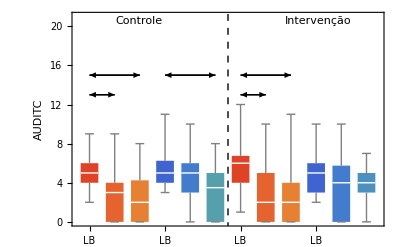

```mathematica
Clear[errorBar2];

caso="completo";
var="AUDITC" ;
shortname="audc";
maxplot=21;
exportaGraficos[bbariscolb]
```

{{LB,{F,M},{I,C,I,C},{13.359,10.0816,10.1111,10.1379}},{z6,{F,M},{I,C,I,C},{3.93548,3.52381,4.73684,5.81818}},{z12,{F,M},{I,C,I,C},{3.48148,3.,4.28571,4.55556}},{LB,{C,I},{F,M,F,M},{0.0155912,0.984663}},{z6,{C,I},{F,M,F,M},{0.995442,0.383697}},{z12,{C,I},{F,M,F,M},{0.720757,0.83323}}}

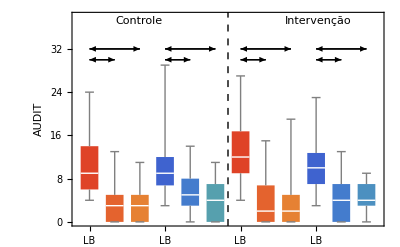

```mathematica
caso="completo";
var="AUDITESC";
shortname="audesc";
maxplot=38;
exportaGraficos[bbariscolb]
```

### Agora só mantemos os que responderam todos os ítens

{{LB,{F,M},{I,C,I,C},{5.88889,4.7027,4.64286,5.22222}},{z6,{F,M},{I,C,I,C},{2.81481,3.02703,3.92857,4.38889}},{z12,{F,M},{I,C,I,C},{2.48148,2.59459,3.71429,3.27778}},{LB,{C,I},{F,M,F,M},{0.0401631,0.343155}},{z6,{C,I},{F,M,F,M},{0.549333,0.670536}},{z12,{C,I},{F,M,F,M},{0.574114,0.621117}}}

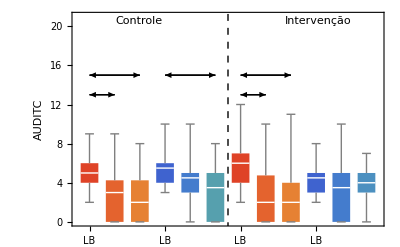

```mathematica
caso="parcial";
var="AUDITC";
shortname="audc";
varwaves={var,"z6"<>var,"z12"<>var};
maxplot=21;
exportaGraficos[bbariscoz12]
```

### Agora para AUDITESC

{{LB,{F,M},{I,C,I,C},{13.0741,9.2973,8.71429,9.11111}},{z6,{F,M},{I,C,I,C},{3.81481,3.7027,4.78571,5.27778}},{z12,{F,M},{I,C,I,C},{3.48148,3.,4.28571,4.55556}},{LB,{C,I},{F,M,F,M},{0.0115803,0.828671}},{z6,{C,I},{F,M,F,M},{0.597664,0.726246}},{z12,{C,I},{F,M,F,M},{0.720757,0.83323}}}

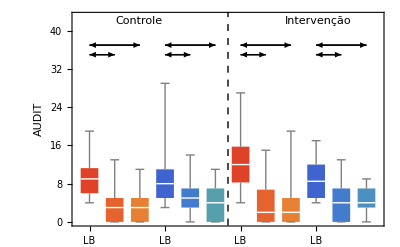

```mathematica
caso="parcial";
var="AUDITESC";
shortname="audesc";
varwaves={var,"z6"<>var,"z12"<>var};
maxplot=43;
exportaGraficos[bbariscoz12]
```

### Frequência

```mathematica
len=Length[bbariscoz12];
caso="parcial";
var="AFQBEB10";
shortname="audesc";
varwaves={var,"z6"<>var,"z12"<>var};
```

#### Inicial

```mathematica
datasetcontrolez1=Select[bbariscolb,#GRUPO=="C"&];
datasetintervencaoz1=Select[bbariscolb,#GRUPO=="I"&];
tabciz1=Append[Table[Flatten[{hashfreq[value],geraporcento2[datasetcontrolez1,#AFREQBEB==value&],geraporcento2[datasetintervencaoz1,#AFREQBEB==value&],geraporcento2[bbariscolb,#AFREQBEB==value&]}],{value,0,4}],
{"Total",Length[datasetcontrolez1],100,Length[datasetintervencaoz1],100,Length[bbariscolb],100}];
```

#### Seis Meses

```mathematica
datasetcontrolez6=Select[bbariscoz6,#GRUPO=="C"&];
datasetintervencaoz6=Select[bbariscoz6,#GRUPO=="I"&];
tabciz6=Append[Table[Flatten[{hashfreq[value],geraporcento2[datasetcontrolez6,#z6FREQBE==value&],geraporcento2[datasetintervencaoz6,#z6FREQBE==value&],geraporcento2[bbariscoz6,#z6FREQBE==value&]}],{value,0,4}],{"Total",Length[datasetcontrolez6],100,Length[datasetintervencaoz6],100,Length[bbariscoz6],100}];
```

#### Doze Meses

```mathematica
datasetcontrolez12=Select[bbariscoz12,#GRUPO=="C"&];
datasetintervencaoz12=Select[bbariscoz12,#GRUPO=="I"&];
tabciz12=Append[Table[Flatten[{hashfreq[value],geraporcento2[datasetcontrolez12,#z12FREQB==value&],geraporcento2[datasetintervencaoz12,#z12FREQB==value&],geraporcento2[bbariscoz12,#z12FREQB==value&]}],{value,0,4}],{"Total",Length[datasetcontrolez12],100,Length[datasetintervencaoz12],100,Length[bbariscoz12],100}];
```

```mathematica
tab=geraTabVar[{{tabciz1,"Linha de Base"},{tabciz6,"6 Meses"},{tabciz12,"12 Meses"}},"Frequ\\^encia com que bebeu 30 dias "<>geraSize[len],2];
Export[prefix<>"tabVarFreq.tex",tab,"String"];
compilaTex[tab,prefix]
```

-Graphics-

### Maior Dose Consumida

```mathematica
tabciz1=Append[Table[Flatten[{hashaoc[value],geraporcento2[datasetcontrolez1,#AOCMAISB==value&],geraporcento2[datasetintervencaoz1,#AOCMAISB==value&],geraporcento2[bbariscolb,#AOCMAISB==value&]}],{value,0,3}],
{"Total",Length[datasetcontrolez1],100,Length[datasetintervencaoz1],100,Length[bbariscolb],100}];
```

#### Seis Meses

```mathematica
datasetcontrolez6=Select[bbariscoz6,#GRUPO=="C"&];
datasetintervencaoz6=Select[bbariscoz6,#GRUPO=="I"&];
tabciz6=Append[Table[Flatten[{hashaoc[value],geraporcento2[datasetcontrolez6,#z6OCMAIS==value&],geraporcento2[datasetintervencaoz6,#z6OCMAIS==value&],geraporcento2[bbariscoz6,#z6OCMAIS==value&]}],{value,0,3}],{"Total",Length[datasetcontrolez6],100,Length[datasetintervencaoz6],100,Length[bbariscoz6],100}];
```

#### Doze Meses

```mathematica
datasetcontrolez12=Select[datasetz12,#GRUPO=="C"&];
datasetintervencaoz12=Select[datasetz12,#GRUPO=="I"&];
datasettotalz12=Select[datasetz12,#GRUPO=="I" || #GRUPO=="C"&];
tabciz12=Append[Table[Flatten[{hashaoc[value],geraporcento2[datasetcontrolez12,#z12OCMAB==value&],geraporcento2[datasetintervencaoz12,#z12OCMAB==value&],geraporcento2[bbariscoz12,#z12OCMAB==value&]}],{value,0,3}],{"Total",Length[datasetcontrolez12],100,Length[datasetintervencaoz12],100,Length[bbariscoz12],100}];
```

```mathematica
tab=geraTabVar[{{tabciz1,"Linha de Base"},{tabciz6,"6 Meses"},{tabciz12,"12 Meses"}},"Maior Dose Consumida "<>geraSize[len],2];
Export[prefix<>"tabVarAOC.tex",tab,"String"];
compilaTex[tab,prefix]
```

-Graphics-

Attrition

```mathematica
var1=#SEXOS&;
var2=ToString[#"RecusaIB6"==0 && #RecusaIB12==0]&;
fline[data_,var_,size_]:={Length[data],N[100*Length[data]/size],N[Mean[data[All,var]]],N[StandardDeviation[data[All,var]]]}
fline2[data_,size_]:={Length[data],N[100*Length[data]/size],N[Mean[data]],N[StandardDeviation[data]]}
statname={"N","\\%" ,"$\\mu$","$\\sigma$","p-value"};
assocnamesgroups=<|"True"->"N\\~ao Abandonou","False"->"Abandonou","Total"->"Total"|>;
geraFilesAttrition[{var_,varname_,maxplot_}]:=Module[
{assocAtt,assocAttTex,g1,part2},
assocAtt=geraassocAttrition[bbariscolb,var1,var2,var, fline2];
assocAttTex=geraassocAttTex[assocvarnamesShortTex[var],assocAtt,2,statname,assocnamesgroups];
Export[prefix<>"tabattrition"<>varname<>".tex",assocAttTex,"String"];
part2=KeySort[data[GroupBy[var1],GroupBy[var2]]];
g1=geraGraficoAttrition[var,part2,maxplot] ;

Export[prefix<>"attrition"<>varname<>".pdf",g1];
{g1,compilaTex[assocAttTex,prefix]}
]
```

```mathematica
maxplot=15;

GraphicsGrid[geraFilesAttrition[#]&/@
{{"AUDITC","audc",15},{"AUDITESC","audesc",45},{"DROGAS12","drogas",10}}]
```

-Graphics-

Correlação entre Uso de Alcool e uso de Drogas

```mathematica
geracorrtabs[dataset_,lisvar_]:=Module[{corrtab,corrtabteste,corrtabTex},
corrtab=geracorrtab[dataset,lisvar];
corrtabteste=geracorrtabteste[dataset,lisvar];
corrtabTex=geracorrtabTex[corrtab,corrtabteste,lisvar];
Export[prefix<>"corrdrogasaudc.tex",corrtabTex, "String"];
compilaTex[corrtabTex,prefix]
]
```

```mathematica
GraphicsColumn[geracorrtabs[bbariscoz12,#]&/@{{"AUDITC","DROGAS30","DROGAS12","z6AUDITC","z6DROGAS30","z12AUDITC","z12DROGAS30"},{"AUDITESC","DROGAS30","DROGAS12","z6AUDITESC","z6DROGAS30","z12AUDITESC","z12DROGAS30"}}]
```

-Graphics-

Regressão à Média

### Caso Gaussiano

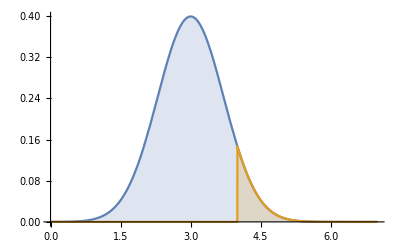

```mathematica
Plot[{1/(Sqrt[2 π]) Exp[-(x-3)^2],If[x>4 ,1/(Sqrt[2 π]) Exp[-(x-3)^2],0]},{x,0,7},Filling->Axis,PlotRange->All]
```

O objetivo é estimar a variação da média ao escolhermos indivíduos com variável x>L e no caso onde as medidas  não estão correlacionadas e obedecem a mesma distribuição. Esse efeito é denotado pela variável E.

-Graphics-

A quantidade E pode ser calculada através de:

E=(∫_L^∞ x PDF(x)ⅆx)/(∫_L^∞ PDF(x)ⅆx)-μ

No Caso de uma Normal temos:

-μ+(√(2/π) (ⅇ^(-(L-μ)^2/(2 σ^2)) σ^2+√(π/2) μ σ Erfc[(L-μ)/(√2 σ)]))/(σ Erfc[(L-μ)/(√2 σ)])
Que pode ser simplificado como: 

σ (ϕ(z))/(Φ(z))
onde ϕ é a PDF da Normal Φ é a CDF e 

z=(c-μ)/σ

No caso com dados correlacionados temos:



E=σ_w^2/(√(σ_b^2+σ_w^2))(ϕ(z))/(Φ(z))

σ_t^2 = σ_b^2+σ_w^2

z=(c-μ)/σ_t

σ_b^2=ρ σ_t^2

Temos que 

σ_w^2=σ_t^2 - σ_b^2=σ_t^2-ρ σ_t^2
      =(1-ρ)σ_t^2
      

E=(1-ρ) (ϕ (z))/Φ(z)σ_t

Vamos definir uma função que estime o efeito sobre uma distribuição experimental.

#### Simulação

Vamos testar o caso ρ=0

Vamos testar essa expressão gerando um conjunto de dados gerados por simulação de Monte Carlo.

```mathematica
μ=1.5;
σ=2;
L=4;
lispiloto=Table[RandomVariate[NormalDistribution[μ,σ]],{1000}];
lispart=Select[lispiloto,#>L&];
liswave=Table[RandomVariate[NormalDistribution[μ,σ]],{Length[lispart]}];
{Mean[lispart]-Mean[lispiloto],calcEfeito[lispiloto,L,0]}
```

{3.51276,3.49339}

Só para constar vamos aplicar isso nos nossos dados.

```mathematica
lisRTM=Cases[Normal[dataset1[All,"AUDITESC"]],_Integer]//N;
L=4;
z=(L-Mean[lisRTM])/StandardDeviation[lisRTM];
ρ=Abs[geraCorr[dataset1,"AUDITESC","z6AUDITESC"][[1]]];
μ=Mean[lisRTM];
σ=StandardDeviation[lisRTM];
efeito=calcEfeito[lisRTM,L,ρ];
efeito/Abs[Mean[bbacomp[All,"z6AUDITESC"]]-Mean[bbacomp[All,"AUDITESC"]]//N]
```

0.723247

```mathematica
lisRTM=Cases[Normal[dataset1[All,"AUDITESC"]],_Integer]//N;
lisRTMC=Cases[Normal[dataset1[All,"AUDITC"]],_Integer]//N;
```

### Caso Exponencial

```mathematica
partlsd=Delete[Select[#,#RECUSAIB==0&&#RecusaIB12==0&]&/@(Delete[GroupBy[Select[dataset1,#RECUSA==0&],{#GRUPO}&],1]),1];
liscontrole=(Cases[Normal[partlsd[[1]][All,"AUDITESC"]],_Integer]//N);
lisintervencao=(Cases[Normal[partlsd[[2]][All,"AUDITESC"]],_Integer]//N);
liscontrole1=(Cases[Normal[partlsd[[1]][All,"z1AUDITESC"]],_Integer]//N);
lisintervencao1=(Cases[Normal[partlsd[[2]][All,"z1AUDITESC"]],_Integer]//N);
liscontrolez6=(Cases[Normal[partlsd[[1]][All,"z6AUDITESC"]],_Integer]//N);
lisintervencaoz6=(Cases[Normal[partlsd[[2]][All,"z6AUDITESC"]],_Integer]//N);
liscontrolez12=(Cases[Normal[partlsd[[1]][All,"z12AUDITESC"]],_Integer]//N);
lisintervencaoz12=(Cases[Normal[partlsd[[2]][All,"z12AUDITESC"]],_Integer]//N);
```

Vamos represntar nossos dados, junto com um ajuste linear. A linearidade da curva mostra de forma clara que os dados são distribuídos como um exponencial.

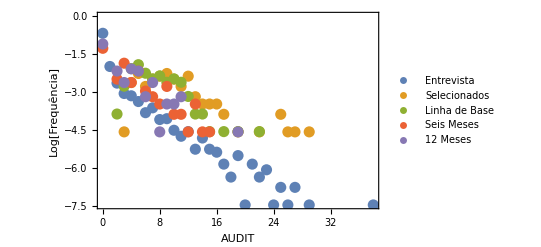

```mathematica
gr1=ListPlot[{Tally[lisRTM]/.{x_,y_}->{x,Log[y/Length[lisRTM]]},
Tally[Join[liscontrole,lisintervencao]]/.{x_,y_}->{x,Log[y/Length[Join[liscontrole,lisintervencao]]]},
Tally[Join[liscontrole1,lisintervencao1]]/.{x_,y_}->{x,Log[y/Length[Join[liscontrole1,lisintervencao1]]]},
Tally[Join[liscontrolez6,lisintervencaoz6]]/.{x_,y_}->{x,Log[y/Length[Join[liscontrolez6,lisintervencaoz6]]]},Tally[Join[liscontrolez12,lisintervencaoz12]]/.{x_,y_}->{x,Log[y/Length[Join[liscontrolez12,lisintervencaoz12]]]}},PlotStyle->PointSize[0.02],PlotLegends->PointLegend[{"Entrevista", "Selecionados","Linha de Base","Seis Meses","12 Meses"}],Frame->True, FrameLabel->{Style["AUDIT",FontSize->18],Style["Log[Frequência]",FontSize->18]}]
```

```mathematica
lm=LinearModelFit[Tally[Join[liscontrolez6,lisintervencaoz6]]/.{x_,y_}->{x,Log[y/Length[Join[liscontrolez6,lisintervencaoz6]]]},x,x]
```

FittedModel[-1.56848-0.202856 x]

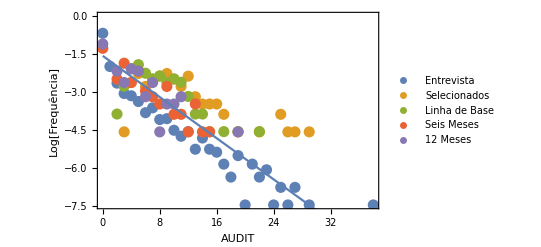

```mathematica
gr4=Plot[Normal[lm],{x,0,35}];
gr5=Show[{gr1,gr4}]
```

```mathematica
Export[prefix<>"expdist.pdf",gr5]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/expdist.pdf

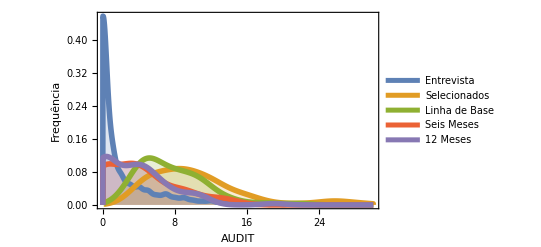

```mathematica
SmoothHistogram[{lisRTM,Join[liscontrole,lisintervencao],Join[liscontrole1,lisintervencao1],Join[liscontrolez6,lisintervencaoz6],Join[liscontrolez12,lisintervencaoz12]},PlotLegends->LineLegend[{"Entrevista", "Selecionados","Linha de Base","Seis Meses","12 Meses"}],Axes->True, PlotRange->{{0,30},All},Filling->Bottom,PlotStyle->{Thickness[0.01]},Frame->True, FrameLabel->{Style["AUDIT",FontSize->18],Style["Frequência",FontSize->18]}]
```

```mathematica
scale=N[Floor[10*(HistogramList[lisRTM][[2,1]])/Length[lisRTM]]/10];
max=1.1;
listicksy=Table[{max*i/5,scale*i/5},{i,0,5}];
```

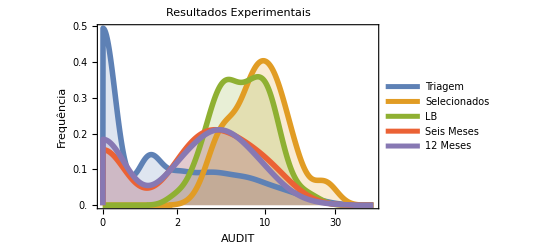

```mathematica
gr1=SmoothHistogram[Log[#+1]&/@{lisRTM,Join[liscontrole,lisintervencao],Join[liscontrole1,lisintervencao1],Join[liscontrolez6,lisintervencaoz6],Join[liscontrolez12,lisintervencaoz12]},PlotLegends->LineLegend[{"Triagem","Selecionados","LB", "Seis Meses","12 Meses"}],Axes->True,PlotRange->{{0,4},All},Filling->Bottom,PlotStyle->{Thickness[0.01]},Frame->True, FrameLabel->{Style["AUDIT",FontSize->18],Style["Frequência",FontSize->18]},FrameTicks->{listicksy,{{0,{Log[1+1],1},{Log[3],2},{Log[6],5},{Log[11],10},{Log[21],20},{Log[31],30},{Log[51],50}},None}},PlotLabel->Style["Resultados Experimentais", "FontSize"->16]]
```

```mathematica
Export[prefix<>"logdist.pdf",gr1]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/logdist.pdf

No caso de uma distribuição exponencial

PDF(x)=e^(-β x)/β

Podemos testar essa previão nos nossos dados:

```mathematica
Exp[lm["BestFitParameters"][[1]]]

β=-lm["BestFitParameters"][[2]]
```

0.208361

0.202856

Note que aplicamos o logaritmo antes de realizar a modelagem.

Outra hipótese testável é que os casos mais extremos,θ,observados devem obeder a equação:

N e^(-β θ)/β ∼1
-β θ=Log(β/N)

θ=-1/βLog(β/N)

```mathematica
-Log[β/2000]/β
```

45.3334

```mathematica
-Log[β/84]/β
```

29.7062

Comparando com os dados observamos que esses resultados 
são compatíveis com os dados empíricos. O que fortalece a idéia de que essa distribuição é exponencial.

Vamos generalizar os resultados anteriores para esse caso:

E=(∫_L^∞ x PDF(x)ⅆx)/(∫_L^∞ PDF(x)ⅆx)-μ

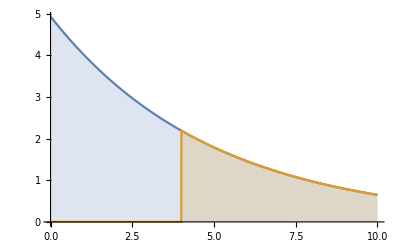

-Graphics-

```mathematica
Plot[{(1/β) Exp[-β x],If[x>4 ,(1/β) Exp[-β x],0]},{x,0,10},Filling->Axis,PlotRange->All]
```

```mathematica
Clear[L,μ,σ,x,β];
Integrate[x 1/β Exp[-β x], {x,L,∞},Assumptions->{σ>0}]/Integrate[1/β Exp[-β x],{x,L,∞},Assumptions->{σ>0}]-Integrate[x 1/β Exp[-β x], {x,0,∞},Assumptions->{β>0}]/Integrate[1/β Exp[-β x],{x,0,∞},Assumptions->{Re[β]>0}]
```

ConditionalExpression[-1/β+(1+L β)/β,Re[β]>0]

```mathematica
Simplify[-1/β+(1+L β)/β]
```

L

Calculamos também o desvio padrão desse caso.

```mathematica
Clear[L,μ,σ,x];
Integrate[x^2 1/β Exp[-β x], {x,L,∞},Assumptions->{σ>0}]/Integrate[1/β Exp[-β x],{x,L,∞},Assumptions->{σ>0}]-(Integrate[x 1/β Exp[-β x], {x,L,∞},Assumptions->{β>0}]/Integrate[1/β Exp[-β x],{x,L,∞},Assumptions->{Re[β]>0}])^2
```

ConditionalExpression[-(1+L β)^2/β^2+(2+L β (2+L β))/β^2,Re[β]>0]

```mathematica
Sqrt[Simplify[-(1+L β)^2/β^2+(2+L β (2+L β))/β^2]]
```

√(1/β^2)

Esse resultado mostra que efeito é  L e o desvio é igual a 1/β. Na tabela abaixo reunimos esses resultados.

```mathematica
Clear[μ,σ,L,β]
Grid[{ {"Distribuição", μ , σ},
{"Exponencial", 1/β,1/β},
{"Exp. com Limiar",L+1/β,1/β}},Dividers->All
]
```

Distribuição | μ | σ
Exponencial | 1/β | 1/β
Exp. com Limiar | L+1/β | 1/β

Podemos comparar com os resultados de simulações de Monte Carlo.

```mathematica
λ=β;
β=0.2;
L=4;
lispiloto=Table[RandomVariate[ExponentialDistribution[λ]],{1000}];
lispart=Select[lispiloto,#>L&];
liswave=Table[RandomVariate[ExponentialDistribution[λ]],{Length[lispart]}];
{Mean[lispart]-Mean[lispiloto],L}
```

{4.36409,4}

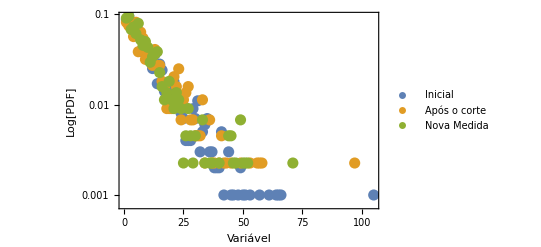

```mathematica
ListLogPlot[N[BinCounts[#,0.5]/Length[#]&/@{lispiloto,lispart,liswave}],PlotStyle->PointSize[0.02],PlotLegends->PointLegend[{"Inicial", "Após o corte","Nova Medida"}],Frame->True, FrameLabel->{Style["Variável",FontSize->18],Style["Log[PDF]",FontSize->18]}]
```

```mathematica
fefeito=fefeito=calcEfeito[lisRTM,4,0]/Abs[Mean[Join[liscontrole,lisintervencao]]-Mean[Join[liscontrolez6,lisintervencaoz6]]//N];
dist=Table[
L=4;
λ=0.209;
lispiloto=Table[RandomVariate[ExponentialDistribution[λ]],{84}];
lispart=Select[lispiloto,#>L&];
liswave=Table[RandomVariate[ExponentialDistribution[λ]],{Length[lispart]}];
L/(Mean[lispart]-Mean[lispiloto]),{10000}];
pvalue=Length[Select[dist,#<fefeito&]]/Length[dist]//N;
```

```mathematica
fefeito
```

0.747371

```mathematica
StringTemplate["A fração do efeito nesse caso explicada por RTM é `fracao`. Podemos através de uma simulação de Monte Carlo estimar a significância Estatísitca desse resultado em `pvalue`. Conclusão 
o efeito medido é maior que o esperado. "][<| "fracao"->fefeito,"pvalue"->pvalue|>]
```

A fração do efeito nesse caso explicada por RTM é 0.74737139. Podemos através de uma simulação de Monte Carlo estimar a significância Estatísitca desse resultado em 0.022. Conclusão 
o efeito medido é maior que o esperado.

```mathematica
fefeito=calcEfeito[lisRTM,4,0]/Abs[Mean[Join[liscontrole,lisintervencao]]-Mean[lisRTM]//N]
```

0.584771

```mathematica
fefeito=calcEfeito[lisRTM,4,0]
```

4.52315

```mathematica
Abs[Mean[Join[liscontrole,lisintervencao]]-Mean[Join[liscontrolez6,lisintervencaoz6]]]
```

6.05208

```mathematica
calcEfeito[lisRTM,4,0]
```

4.52315

```mathematica
1/2.5
```

0.4

```mathematica
frametext=Style[#,"FontSize"->14]&/@{"fração do efeito","PDF"};
gr1=SmoothHistogram[dist,Filling->Bottom,PlotRange->{{fefeito,1.8},All},Frame->True];
gr2=SmoothHistogram[dist,Filling->Bottom,PlotRange->{{0,fefeito},All},PlotStyle->Orange];
gr3=SmoothHistogram[dist,PlotRange->{All,All},PlotStyle->Orange,Frame->True,FrameLabel-> frametext];
Export[prefix<>"pvalue.pdf",Show[gr3,gr2,gr1]]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/pvalue.pdf

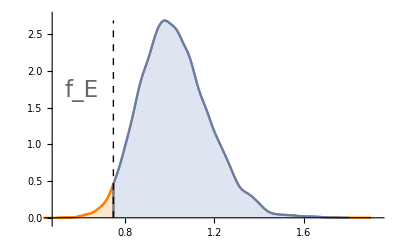

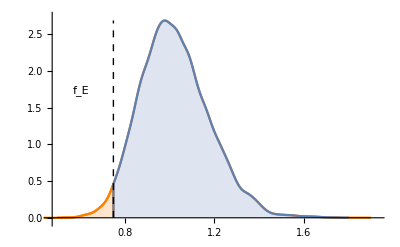

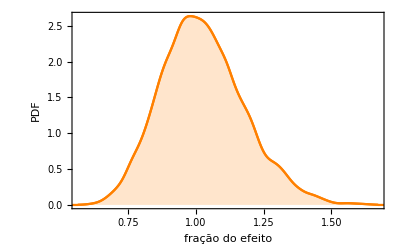

```mathematica
Show[gr3,gr2,gr1]
```

### Grupo Risco mais Restrito

```mathematica
bbariscorest=Select[bbarisco,#AUDITESC≥8 &&( #GRUPO=="C"|| #GRUPO=="I")&&#RECUSA==0 &&#RecusaIB6==0&];
```

```mathematica
(bbariscorest[All,"z6AUDITESC"]//Mean//N)
```

4.32911

```mathematica
(bbariscorest[All,"AUDITESC"]//Mean//N)
```

12.7342

```mathematica
(bbariscorest[All,"AUDITESC"]//Mean//N)-(bbariscorest[All,"z6AUDITESC"]//Mean//N)
```

8.40506

```mathematica
calcEfeito[lisRTM,8,0]
```

7.61034

```mathematica
7.61/8.40
```

0.905952

```mathematica
fefeito=calcEfeito[lisRTM,8,0]/Abs[(bbariscorest[All,"AUDITESC"]//Mean//N)-(bbariscorest[All,"z6AUDITESC"]//Mean//N)];
dist=Table[
L=8;
λ=0.209;
lispiloto=Table[RandomVariate[ExponentialDistribution[λ]],{84}];
lispart=Select[lispiloto,#>L&];
liswave=Table[RandomVariate[ExponentialDistribution[λ]],{Length[lispart]}];
L/(Mean[lispart]-Mean[lispiloto]),{10000}];
pvalue=Length[Select[dist,#<fefeito&]]/Length[dist]//N;
```

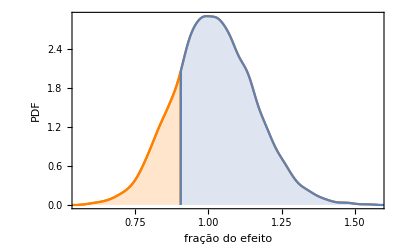

```mathematica
frametext=Style[#,"FontSize"->14]&/@{"fração do efeito","PDF"};
gr1=SmoothHistogram[dist,Filling->Bottom,PlotRange->{{fefeito,1.8},All},Frame->True];
gr2=SmoothHistogram[dist,Filling->Bottom,PlotRange->{{0,fefeito},All},PlotStyle->Orange];
gr3=SmoothHistogram[dist,PlotRange->{All,All},PlotStyle->Orange,Frame->True,FrameLabel-> frametext];
Show[gr3,gr2,gr1]
```

### Análise Linear

### Caso Paradigmático

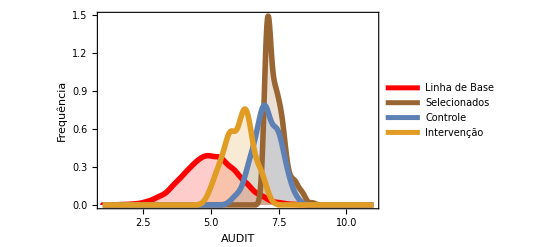

```mathematica
delay=5;
lisinit=Table[RandomVariate[NormalDistribution[delay,1]],{10000}];
lis2=Select[lisinit,#>delay+2&];
lis3=Table[RandomVariate[NormalDistribution[delay+2,0.5]],Floor[Length[lis2]/2]];
lis4=Table[RandomVariate[NormalDistribution[delay+1,0.5]],Floor[Length[lis2]/2]];
grpar=SmoothHistogram[{lisinit,lis2,lis3,lis4},PlotStyle-> {{Thickness[0.01],Red},{Thickness[0.01],Brown},{Thickness[0.01],RGBColor[0.368417,0.506779,0.709798]},{Thickness[0.01],RGBColor[0.880722,0.611041,0.142051]}},PlotLegends->LineLegend[{"Linha de Base","Selecionados",  "Controle","Intervenção"}],Axes->True,PlotRange->{{delay-4,delay+6},All},Filling->Bottom,Filling->Bottom,PlotStyle->{Thickness[0.01]},Frame->True, FrameLabel->{Style["AUDIT",FontSize->18],Style["Frequência",FontSize->18]}]
```

```mathematica
Export[prefix<>"RTMdistpar.pdf",grpar]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/RTMdistpar.pdf

```mathematica
Length[lis2]
```

225

```mathematica
Length/@{Log[(lis3)/lis2[[1;;Length[lis3]]]],Log[lis2[[1;;Length[lis3]]]]}
```

{112,112}

```mathematica
Length/@{Log[(lis4)/lis2[[Length[lis3]+2;;-1]]],Log[lis2[[Length[lis3]+2;;-1]]]}
```

{112,112}

```mathematica
{Transpose[{Log[(lis3)/lis2[[1;;Length[lis3]]]],Log[lis2[[1;;Length[lis3]]]]}],Transpose[{Log[lis4/lis2[[Length[lis3]+2;;-1]]],Log[lis2[[Length[lis3]+2;;-1]]]
}]}
```

{{{-0.1277,2.04473},{-0.277914,2.03559},{-0.119665,2.03356},{-0.0616768,2.10913},{-0.113995,1.98308},{0.0137776,2.00976},{-0.00876661,1.94661},{-0.0850754,2.08979},{-0.100301,2.00681},{0.0192909,1.96098},{-0.0732285,2.01448},{0.00862207,1.98345},{-0.0965386,1.96398},{-0.0620465,2.02769},{0.0215378,2.0032},{-0.100439,2.06373},{-0.0520016,1.99968},{0.0445372,1.94988},{-0.18551,2.09344},{-0.049389,2.02729},{0.129517,1.96467},{-0.0151274,1.94891},{0.0320189,1.97532},{-0.095543,2.01677},{-0.000417239,1.95143},{-0.133862,2.08617},{-0.106873,2.05027},{0.0883744,1.96644},{-0.0441168,1.97541},{-0.126691,1.99665},{-0.0182064,1.96303},{-0.0474766,2.0139},{-0.017874,1.97147},{-0.225694,2.12542},{-0.0456617,1.95147},{0.0341229,2.03915},{0.00685225,1.94745},{-0.0452514,1.98822},{0.0318986,1.9708},{-0.0676665,2.03901},{-0.149999,2.09121},{-0.0881006,1.99772},{-0.148025,2.00687},{0.000848937,2.02132},{0.00938249,1.96249},{-0.0356226,1.98145},{-0.0341961,1.96664},{-0.125218,2.11872},{-0.127562,1.98717},{-0.14963,1.98365},{-0.0601697,1.97509},{0.0656961,1.9526},{-0.015371,2.04121},{-0.0604737,1.99622},{-0.0447144,1.96668},{0.0787049,1.94772},{-0.0123143,2.03241},{-0.062537,1.96319},{-0.00467671,2.0497},{-0.0851245,1.94921},{-0.0235044,2.01274},{0.0195078,1.95984},{-0.0774278,1.96625},{-0.08361,1.96201},{0.00844522,1.94986},{-0.03887,1.99406},{-0.127607,1.9638},{-0.0912996,2.0405},{0.0532798,1.95455},{-0.0498862,1.94689},{-0.0162376,2.00966},{0.0316051,1.99431},{-0.0185471,2.0491},{-0.181468,1.96585},{-0.0639619,1.955},{-0.101446,1.95088},{-0.200499,2.10106},{0.0490587,1.95064},{-0.0394424,2.01504},{0.0384942,1.98814},{0.00425136,2.00549},{0.0597468,1.94753},{-0.0252476,1.95491},{-0.195702,2.03281},{0.0591212,1.95316},{0.0339598,1.97061},{-0.0651487,2.05261},{-0.0431503,1.99214},{-0.120384,1.96215},{-0.280793,2.16899},{-0.00767082,1.97293},{-0.0443232,1.98124},{0.101029,1.9655},{0.101744,1.99726},{-0.169785,1.95697},{-0.0365414,1.9619},{0.0466251,2.01852},{-0.122896,2.01868},{-0.194336,2.00284},{0.110236,1.94884},{-0.177957,2.03623},{0.0597553,1.9893},{0.0124404,1.99302},{-0.0438116,1.99798},{-0.0560461,2.09874},{0.095554,1.95315},{-0.0681995,1.99481},{-0.0882365,1.96083},{-0.111353,2.02534},{-0.186807,2.13722},{-0.00903598,1.95139},{0.00288025,2.0058}},{{-0.248818,2.02268},{-0.226339,2.04594},{-0.265064,2.03402},{-0.0371741,1.97675},{-0.253156,2.00288},{-0.0639559,1.97717},{-0.297571,2.03231},{-0.216632,1.95352},{-0.15978,1.99083},{-0.320251,2.0737},{-0.193302,2.00756},{-0.382632,1.99147},{-0.0760112,2.00406},{-0.149978,1.96008},{-0.362136,2.07357},{-0.205955,2.05948},{-0.29144,2.02581},{-0.318979,2.12363},{-0.24071,2.06524},{-0.367492,2.02013},{-0.383199,2.13204},{-0.143536,1.95324},{-0.146162,2.04477},{-0.313281,2.00088},{-0.259212,1.95864},{-0.16863,2.0239},{-0.27537,2.02659},{-0.207666,2.06297},{-0.164963,1.95171},{-0.443184,2.07274},{-0.167366,2.11391},{-0.0769787,1.95989},{-0.446612,2.08782},{-0.093196,1.96495},{-0.270591,1.95109},{-0.151038,1.95675},{-0.267237,1.95857},{-0.202558,1.9478},{-0.105782,2.03186},{-0.234701,1.97104},{-0.236082,2.02996},{-0.035102,1.95209},{-0.427344,2.01777},{-0.0969174,1.96821},{-0.00174543,1.95932},{-0.148625,2.00422},{-0.397,2.08573},{-0.1593,2.01814},{-0.312953,1.98881},{-0.164352,1.98502},{-0.230687,2.06511},{-0.156276,2.03452},{-0.144759,2.00165},{-0.166365,1.95651},{-0.0149873,1.94817},{-0.17537,2.00371},{-0.250304,2.03167},{-0.318727,2.03011},{-0.142134,1.95977},{-0.252296,1.95895},{-0.222485,1.9618},{-0.258589,1.96728},{-0.220424,1.96024},{-0.350254,2.0014},{-0.339296,1.94986},{-0.142839,1.96634},{-0.217612,1.96475},{-0.117495,1.96847},{-0.216565,1.96363},{-0.109402,1.95544},{-0.194895,2.04967},{-0.124419,1.97674},{-0.248082,1.97203},{-0.0710808,1.96704},{-0.210935,2.01683},{-0.0285598,1.96339},{-0.0444083,1.9637},{-0.170846,1.94728},{-0.163754,1.94869},{-0.197943,2.04041},{-0.155756,1.96444},{-0.0656197,1.96779},{-0.216531,2.02719},{-0.168134,2.02307},{-0.314531,1.98608},{-0.199716,1.94859},{-0.152416,1.98781},{-0.177639,2.00198},{-0.250141,2.06107},{-0.18889,1.94717},{-0.0403859,1.95104},{-0.0495803,1.94899},{-0.225713,1.97098},{-0.114383,1.97761},{-0.126063,1.94665},{-0.321697,1.97707},{-0.349758,1.99886},{-0.132967,1.96224},{-0.188975,2.04452},{-0.26867,2.01534},{-0.351873,2.10222},{-0.274093,1.99942},{-0.117965,1.98635},{-0.249263,2.08458},{-0.158898,2.00432},{-0.25078,1.966},{-0.101077,1.95736},{-0.0804786,1.9493},{-0.234188,2.02482},{-0.17992,2.00832},{-0.119133,1.955},{-0.319624,1.98841}}}

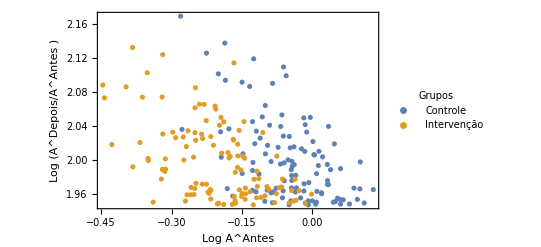

```mathematica
ListPlot[{Transpose[{Log[(lis3)/lis2[[1;;Length[lis3]]]],Log[lis2[[1;;Length[lis3]]]]}],Transpose[{Log[lis4/lis2[[Length[lis3]+2;;-1]]],Log[lis2[[Length[lis3]+2;;-1]]]
}]},Frame->True,PlotStyle->PointSize->0.02,FrameLabel->{Style["Log A^Antes",FontSize->14],Style["Log (A^Depois/A^Antes )",FontSize->14]},
PlotStyle->{RGBColor[0.368417,0.506779,0.709798],Green},PlotLegends->PointLegend[Automatic,{"Controle","Intervenção"},LegendFunction->"Frame",LegendLabel->Style["Grupos",Bold],LegendMarkers->●]]
```

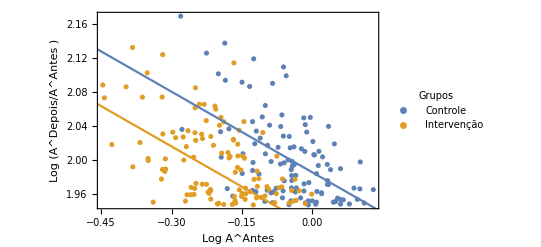

```mathematica
grpoints=ListPlot[{Transpose[{Log[(lis3)/lis2[[1;;Length[lis3]]]],Log[lis2[[1;;Length[lis3]]]]}],Transpose[{Log[lis4/lis2[[Length[lis3]+2;;-1]]],Log[lis2[[Length[lis3]+2;;-1]]]
}]},Frame->True,PlotStyle->PointSize->0.02,FrameLabel->{Style["Log A^Antes",FontSize->14],Style["Log (A^Depois/A^Antes )",FontSize->14]},
PlotStyle->{RGBColor[0.368417,0.506779,0.709798],Green},PlotLegends->PointLegend[Automatic,{"Controle","Intervenção"},LegendFunction->"Frame",LegendLabel->Style["Grupos",Bold],LegendMarkers->●]];
{a1,b1}=LinearModelFit[Transpose[{Log[(lis3)/lis2[[1;;Length[lis3]]]],Log[lis2[[1;;Length[lis3]]]]}],x,x]["BestFitParameters"];
{a2,b2}=LinearModelFit[Transpose[{Log[lis4/lis2[[Length[lis3]+2;;-1]]],Log[lis2[[Length[lis3]+2;;-1]]]}],x,x]["BestFitParameters"];
grfunc=Plot[{a1+b1 x,a2-0.03+b1 x},{x,-1,1},PlotStyle-> {{Automatic},{Automatic},{Black,Dashed}}];
Show[grpoints,grfunc]
```

```mathematica
Export[prefix<>"RTMpar.pdf",Show[grpoints,grfunc]]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/RTMpar.pdf

```mathematica
partlsd=Delete[Select[#,#RECUSAIB==0&&#RecusaIB12==0&]&/@(Delete[GroupBy[Select[dataset1,#RECUSA==0&],{#GRUPO}&],1]),1];
liscontrole=(Cases[Normal[partlsd[[1]][All,"AUDITESC"]],_Integer]//N);
lisintervencao=(Cases[Normal[partlsd[[2]][All,"AUDITESC"]],_Integer]//N);
liscontrole1=(Cases[Normal[partlsd[[1]][All,"z1AUDITESC"]],_Integer]//N);
lisintervencao1=(Cases[Normal[partlsd[[2]][All,"z1AUDITESC"]],_Integer]//N);
liscontrolez6=(Cases[Normal[partlsd[[1]][All,"z6AUDITESC"]],_Integer]//N);
lisintervencaoz6=(Cases[Normal[partlsd[[2]][All,"z6AUDITESC"]],_Integer]//N);
liscontrolez12=(Cases[Normal[partlsd[[1]][All,"z12AUDITESC"]],_Integer]//N);
lisintervencaoz12=(Cases[Normal[partlsd[[2]][All,"z12AUDITESC"]],_Integer]//N);
```

{0.857731,-0.218604,-0.769484}

{{-0.140028,1.85549},{-0.599395,0.162187},{-1.20054,-0.338432}}

| DF | SS | MS | F-Statistic | P-Value
treatment | 1 | 2.98058 | 2.98058 | 3.5983 | 0.060942
time | 1 | 10.4092 | 10.4092 | 12.5664 | 0.000616863
Error | 93 | 77.0347 | 0.82833 |  | 
Total | 95 | 90.4244 |  |  |

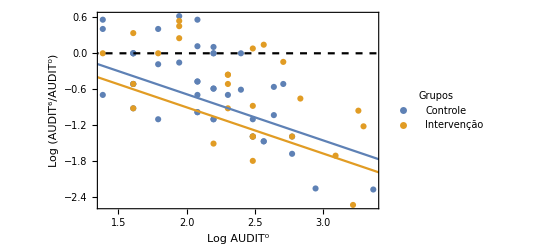

```mathematica
lisAncova=geralisAncova[liscontrole+1,lisintervencao+1,liscontrolez6+1,lisintervencaoz6+1];
lisintervencao2=lisintervencaoz6;
liscontrole2=liscontrolez6;
lislogcontrole=Select[Transpose@{Log[liscontrole],-Log[liscontrole]+Log[liscontrole2]},#[[1]]≠-∞&];
lislogintervencao=Select[Transpose@{Log[lisintervencao],-Log[lisintervencao]+Log[lisintervencao2]},#[[1]]≠-∞&];
grpoints=ListPlot[{lislogcontrole,lislogintervencao},Frame->True,PlotStyle->PointSize->0.02,FrameLabel->{Style["Log AUDIT^0",FontSize->14],Style["Log (AUDIT^6/AUDIT^0)",FontSize->14]},PlotLegends->PointLegend[Automatic,{"Controle","Intervenção"},LegendFunction->"Frame",LegendLabel->Style["Grupos",Bold],LegendMarkers->●]];
lm=LinearModelFit[lisAncova,{treatment,time},{treatment,time}];
{α,β,γ}=lm["BestFitParameters"]
lm["ParameterConfidenceIntervals"]
lm["ANOVATable"]
grfunc=Plot[{α+γ x,α+β+γ x,0},{x,1.,3.5},PlotStyle-> {{Automatic},{Automatic},{Black,Dashed}}];
Show[grpoints,grfunc]
Export[prefix<>"RTMz6.pdf",Show[grpoints,grfunc]];
tabparam={
lm["BestFitParameters"],
lm["ParameterConfidenceIntervals"],lm["ParameterPValues"]};
tabparamTex=geraFitTabTex[tabparam,{"Constante", "Tratamento", "Tempo"}];
Export[prefix<>"tabparamRTMz6.tex",tabparamTex, "String"];
```

```mathematica
compilaTex[tabparamTex,prefix]c
```

c -Graphics-

{1.20717,-0.0220345,-1.01167}

{{0.199227,2.21512},{-0.406713,0.362644},{-1.44712,-0.576217}}

| DF | SS | MS | F-Statistic | P-Value
treatment | 1 | 0.967568 | 0.967568 | 1.14461 | 0.28745
time | 1 | 17.9926 | 17.9926 | 21.2847 | 0.0000126296
Error | 93 | 78.6155 | 0.845328 |  | 
Total | 95 | 97.5756 |  |  |

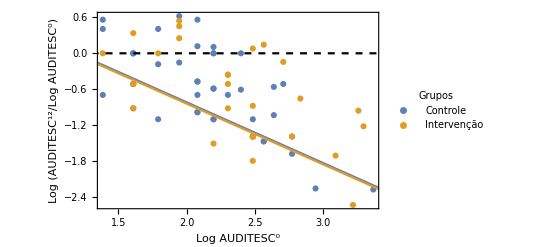

```mathematica
lisAncova=geralisAncova[liscontrole+1,lisintervencao+1,liscontrolez12+1,lisintervencaoz12+1];
lisintervencao2=lisintervencaoz12;
liscontrole2=liscontrolez12;
grpoints=ListPlot[{lislogcontrole,lislogintervencao},Frame->True,PlotStyle->PointSize->0.02,FrameLabel->{Style["Log AUDITESC^0",FontSize->14],Style["Log (AUDITESC^12/Log AUDITESC^0)",FontSize->14]},PlotLegends->PointLegend[Automatic,{"Controle","Intervenção"},LegendFunction->"Frame",LegendLabel->Style["Grupos",Bold],LegendMarkers->●]];
lm=LinearModelFit[lisAncova,{treatment,time},{treatment,time}];
{α,β,γ}=lm["BestFitParameters"]
lm["ParameterConfidenceIntervals"]
lm["ANOVATable"]
grfunc=Plot[{α+γ x,α+β+γ x,0},{x,1.,3.5},PlotStyle-> {{Automatic},{Automatic},{Black,Dashed}}];
Show[grpoints,grfunc]
Export[prefix<>"RTMz12.pdf",Show[grpoints,grfunc]];
tabparam={
lm["BestFitParameters"],
lm["ParameterConfidenceIntervals"],lm["ParameterPValues"]};
tabparamTex=geraFitTabTex[tabparam,{"Constante","Tratamento","Tempo"}];
Export[prefix<>"tabparamRTMz12.tex",tabparamTex, "String"];
```

```mathematica
compilaTex[tabparamTex,prefix]
```

-Graphics-

Simulação do Modelo pqq

Vamos inicialmente definir as variáveis.

```mathematica
lisRTM=Cases[Normal[dataset1[All,"AUDITESC"]],_Integer]//N;
partlsd=Delete[Select[#,#RECUSAIB==0&&#RecusaIB12==0&]&/@(Delete[GroupBy[Select[dataset1,#RECUSA==0&],{#GRUPO}&],1]),1];
liscontrole=(Cases[Normal[partlsd[[1]][All,"AUDITESC"]],_Integer]//N);
lisintervencao=(Cases[Normal[partlsd[[2]][All,"AUDITESC"]],_Integer]//N);
liscontrole1=(Cases[Normal[partlsd[[1]][All,"z1AUDITESC"]],_Integer]//N);
lisintervencao1=(Cases[Normal[partlsd[[2]][All,"z1AUDITESC"]],_Integer]//N);
liscontrolez6=(Cases[Normal[partlsd[[1]][All,"z6AUDITESC"]],_Integer]//N);
lisintervencaoz6=(Cases[Normal[partlsd[[2]][All,"z6AUDITESC"]],_Integer]//N);
liscontrolez12=(Cases[Normal[partlsd[[1]][All,"z12AUDITESC"]],_Integer]//N);
lisintervencaoz12=(Cases[Normal[partlsd[[2]][All,"z12AUDITESC"]],_Integer]//N);
size=Length[Join[liscontrole,lisintervencao]];
size0=Length[lisRTM];
```

### Geração de um Modelo para o Grupo Risco

A idéia é considerar todos com Audit alto e parte dos com 4<=AUDITESC<8. Empiricamente a fração mais adequada foi de 40%.

```mathematica
lisRTM4=Select[lisRTM,#>=4&];
lisRTM8=Select[lisRTM,#>=8&];
temp=Select[lisRTM,#>=4&&#<8&];
lisRTM45=Join[RandomSample[temp,Floor[Length[temp]/2.5]],lisRTM8];
```

```mathematica
scale=N[Floor[10*(HistogramList[lisRTM][[2,1]])/Length[lisRTM]]/10];
max=1.3;
listicksy=Table[{max*i/5,scale*i/5},{i,0,5}];
```

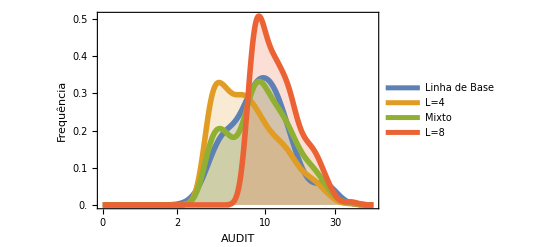

```mathematica
gr2=SmoothHistogram[{Log[Join[liscontrole,lisintervencao]+1],Log[lisRTM4+1],Log[lisRTM45+1],Log[lisRTM8+1]},PlotLegends->LineLegend[{"Linha de Base","L=4",  "Mixto","L=8"}],Axes->True,PlotRange->{{0,4},All},Filling->Bottom,Filling->Bottom,PlotStyle->{Thickness[0.01]},Frame->True, FrameLabel->{Style["AUDIT",FontSize->18],Style["Frequência",FontSize->18]},FrameTicks->{listicksy,{{0,{Log[1+1],1},{Log[3],2},{Log[6],5},{Log[11],10},{Log[21],20},{Log[31],30},{Log[51],50}},None}}]
```

```mathematica
Export[prefix<>"gerarlb.pdf",Show[gr2]]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/gerarlb.pdf

### Determinação dos parâmetros ótimos p e q

Para determinar p e q ótimos. Calculamos a soma cumulativa do Log(f_i+1).

φ_f(k)=∑_(i=0)^k Log(f_i+1)

Essa quantidade foi utilizada pois é finita se f_i=0 e diminui o efeito de concentração das frequências nas proximidades de 0. Para comparar duas distribuições quaisquer usamos uma versão discreta da Métrica de Kolmogorov:

ϵ(f,g)=∑_(k=0)^M |φ_f(k)-φ_g(k)|

onde M é o valor máximo entre os valores presentes em f e em g.

Para determinar o modelo ideal rodamos um programa em python e geramos várias comparações entre as distribuições obtidas por simulação e as distribuições experimentais e determinamos os parâmetros mais próximos.

```mathematica
size0=Length[lisRTM];
size=Length[Join[liscontrole,lisintervencao]];

listDist=ParallelTable[Print[p,",",q];Sum[
simul=Table[Steps[p,q,0,150],{size0}];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
(* Print[sizelocal,",",size,",",Length[simul2]]; *)
simul3=Steps[p,q,#,25]&/@simul2;
       simul4=Steps[p,q,#,25]& /@simul3;
{p,q,compara[simul,lisRTM]},{j,1,100}]/100,{p,0.6,0.99,0.01},{q,0.50,0.65,0.005}];
distListPythonTri=Flatten[listDist,1];
```

0.6,0.5

0.65,0.5

0.7,0.5

0.75,0.5

0.7,0.505

0.65,0.505

0.75,0.505

0.6,0.505

0.7,0.51

0.65,0.51

0.75,0.51

0.6,0.51

0.7,0.515

0.65,0.515

0.75,0.515

0.6,0.515

0.7,0.52

0.65,0.52

0.75,0.52

0.6,0.52

0.7,0.525

0.75,0.525

0.65,0.525

0.6,0.525

0.7,0.53

0.65,0.53

0.75,0.53

0.6,0.53

0.7,0.535

0.65,0.535

0.75,0.535

0.6,0.535

0.7,0.54

0.65,0.54

0.75,0.54

0.6,0.54

0.7,0.545

0.65,0.545

0.75,0.545

0.6,0.545

0.7,0.55

0.65,0.55

0.75,0.55

0.6,0.55

0.7,0.555

0.75,0.555

0.6,0.555

0.65,0.555

0.7,0.56

0.65,0.56

0.75,0.56

0.6,0.56

0.7,0.565

0.75,0.565

0.65,0.565

0.6,0.565

0.7,0.57

0.75,0.57

0.65,0.57

0.6,0.57

0.7,0.575

0.75,0.575

0.65,0.575

0.6,0.575

0.7,0.58

0.75,0.58

0.65,0.58

0.6,0.58

0.7,0.585

0.75,0.585

0.65,0.585

0.6,0.585

0.7,0.59

0.75,0.59

0.65,0.59

0.6,0.59

0.7,0.595

0.75,0.595

0.65,0.595

0.6,0.595

0.7,0.6

0.75,0.6

0.65,0.6

0.6,0.6

0.7,0.605

0.75,0.605

0.65,0.605

0.6,0.605

0.7,0.61

0.75,0.61

0.65,0.61

0.6,0.61

0.7,0.615

0.75,0.615

0.65,0.615

0.6,0.615

0.7,0.62

0.75,0.62

0.65,0.62

0.6,0.62

0.7,0.625

0.75,0.625

0.65,0.625

0.6,0.625

0.7,0.63

0.75,0.63

0.65,0.63

0.6,0.63

0.7,0.635

0.75,0.635

0.65,0.635

0.6,0.635

0.7,0.64

0.75,0.64

0.65,0.64

0.6,0.64

0.7,0.645

0.75,0.645

0.65,0.645

0.6,0.645

0.7,0.65

0.75,0.65

0.65,0.65

0.6,0.65

0.71,0.5

0.76,0.5

0.66,0.5

0.61,0.5

0.71,0.505

0.76,0.505

0.66,0.505

0.61,0.505

0.71,0.51

0.76,0.51

0.66,0.51

0.61,0.51

0.71,0.515

0.76,0.515

0.66,0.515

0.61,0.515

0.71,0.52

0.76,0.52

0.66,0.52

0.61,0.52

0.71,0.525

0.76,0.525

0.66,0.525

0.61,0.525

0.71,0.53

0.76,0.53

0.66,0.53

0.61,0.53

0.71,0.535

0.76,0.535

0.66,0.535

0.61,0.535

0.71,0.54

0.76,0.54

0.66,0.54

0.61,0.54

0.71,0.545

0.76,0.545

0.66,0.545

0.61,0.545

0.71,0.55

0.76,0.55

0.66,0.55

0.61,0.55

0.71,0.555

0.76,0.555

0.66,0.555

0.61,0.555

0.71,0.56

0.76,0.56

0.66,0.56

0.61,0.56

0.71,0.565

0.76,0.565

0.66,0.565

0.61,0.565

0.71,0.57

0.76,0.57

0.66,0.57

0.61,0.57

0.71,0.575

0.76,0.575

0.66,0.575

0.61,0.575

0.71,0.58

0.76,0.58

0.66,0.58

0.61,0.58

0.71,0.585

0.76,0.585

0.66,0.585

0.61,0.585

0.71,0.59

0.76,0.59

0.66,0.59

0.61,0.59

0.71,0.595

0.76,0.595

0.66,0.595

0.61,0.595

0.71,0.6

0.76,0.6

0.66,0.6

0.61,0.6

0.71,0.605

0.76,0.605

0.66,0.605

0.61,0.605

0.71,0.61

0.76,0.61

0.66,0.61

0.61,0.61

0.71,0.615

0.76,0.615

0.66,0.615

0.61,0.615

0.71,0.62

0.76,0.62

0.66,0.62

0.61,0.62

0.71,0.625

0.76,0.625

0.66,0.625

0.61,0.625

0.71,0.63

0.76,0.63

0.66,0.63

0.61,0.63

0.71,0.635

0.76,0.635

0.66,0.635

0.61,0.635

0.71,0.64

0.76,0.64

0.66,0.64

0.61,0.64

0.71,0.645

0.76,0.645

0.66,0.645

0.61,0.645

0.71,0.65

0.76,0.65

0.66,0.65

0.61,0.65

0.72,0.5

0.77,0.5

0.67,0.5

0.62,0.5

0.72,0.505

0.77,0.505

0.67,0.505

0.62,0.505

0.72,0.51

0.77,0.51

0.67,0.51

0.62,0.51

0.72,0.515

0.77,0.515

0.67,0.515

0.62,0.515

0.72,0.52

0.77,0.52

0.67,0.52

0.62,0.52

0.72,0.525

0.77,0.525

0.67,0.525

0.62,0.525

0.72,0.53

0.77,0.53

0.67,0.53

0.62,0.53

0.72,0.535

0.77,0.535

0.67,0.535

0.62,0.535

0.72,0.54

0.77,0.54

0.67,0.54

0.62,0.54

0.72,0.545

0.77,0.545

0.67,0.545

0.62,0.545

0.72,0.55

0.77,0.55

0.67,0.55

0.62,0.55

0.72,0.555

0.77,0.555

0.67,0.555

0.62,0.555

0.72,0.56

0.77,0.56

0.67,0.56

0.62,0.56

0.72,0.565

0.77,0.565

0.67,0.565

0.62,0.565

0.72,0.57

0.77,0.57

0.67,0.57

0.62,0.57

0.72,0.575

0.77,0.575

0.67,0.575

0.62,0.575

0.72,0.58

0.77,0.58

0.67,0.58

0.62,0.58

0.72,0.585

0.77,0.585

0.67,0.585

0.62,0.585

0.72,0.59

0.77,0.59

0.67,0.59

0.62,0.59

0.72,0.595

0.77,0.595

0.67,0.595

0.62,0.595

0.72,0.6

0.77,0.6

0.67,0.6

0.62,0.6

0.72,0.605

0.77,0.605

0.67,0.605

0.62,0.605

0.72,0.61

0.77,0.61

0.67,0.61

0.72,0.615

0.62,0.61

0.77,0.615

0.67,0.615

0.72,0.62

0.62,0.615

0.77,0.62

0.67,0.62

0.72,0.625

0.62,0.62

0.77,0.625

0.67,0.625

0.72,0.63

0.62,0.625

0.77,0.63

0.67,0.63

0.72,0.635

0.62,0.63

0.77,0.635

0.72,0.64

0.67,0.635

0.62,0.635

0.77,0.64

0.72,0.645

0.67,0.64

0.62,0.64

0.77,0.645

0.72,0.65

0.67,0.645

0.62,0.645

0.77,0.65

0.73,0.5

0.67,0.65

0.78,0.5

0.62,0.65

0.73,0.505

0.68,0.5

0.63,0.5

0.78,0.505

0.73,0.51

0.68,0.505

0.63,0.505

0.78,0.51

0.73,0.515

0.68,0.51

0.63,0.51

0.78,0.515

0.73,0.52

0.68,0.515

0.63,0.515

0.78,0.52

0.73,0.525

0.68,0.52

0.63,0.52

0.78,0.525

0.73,0.53

0.68,0.525

0.63,0.525

0.78,0.53

0.73,0.535

0.68,0.53

0.63,0.53

0.78,0.535

0.73,0.54

0.68,0.535

0.63,0.535

0.78,0.54

0.73,0.545

0.68,0.54

0.63,0.54

0.78,0.545

0.73,0.55

0.68,0.545

0.63,0.545

0.78,0.55

0.73,0.555

0.68,0.55

0.63,0.55

0.78,0.555

0.73,0.56

0.68,0.555

0.63,0.555

0.78,0.56

0.73,0.565

0.68,0.56

0.63,0.56

0.78,0.565

0.73,0.57

0.68,0.565

0.63,0.565

0.78,0.57

0.73,0.575

0.68,0.57

0.63,0.57

0.78,0.575

0.73,0.58

0.68,0.575

0.63,0.575

0.78,0.58

0.73,0.585

0.68,0.58

0.63,0.58

0.78,0.585

0.73,0.59

0.68,0.585

0.78,0.59

0.63,0.585

0.73,0.595

0.68,0.59

0.78,0.595

0.63,0.59

0.73,0.6

0.68,0.595

0.78,0.6

0.63,0.595

0.73,0.605

0.68,0.6

0.78,0.605

0.63,0.6

0.73,0.61

0.68,0.605

0.78,0.61

0.63,0.605

0.73,0.615

0.68,0.61

0.78,0.615

0.63,0.61

0.73,0.62

0.78,0.62

0.68,0.615

0.63,0.615

0.73,0.625

0.78,0.625

0.68,0.62

0.63,0.62

0.73,0.63

0.78,0.63

0.68,0.625

0.63,0.625

0.73,0.635

0.78,0.635

0.68,0.63

0.63,0.63

0.73,0.64

0.78,0.64

0.68,0.635

0.63,0.635

0.73,0.645

0.78,0.645

0.68,0.64

0.63,0.64

0.73,0.65

0.78,0.65

0.68,0.645

0.63,0.645

0.74,0.5

0.79,0.5

0.68,0.65

0.63,0.65

0.74,0.505

0.79,0.505

0.69,0.5

0.64,0.5

0.74,0.51

0.79,0.51

0.69,0.505

0.64,0.505

0.74,0.515

0.79,0.515

0.69,0.51

0.64,0.51

0.74,0.52

0.79,0.52

0.69,0.515

0.64,0.515

0.74,0.525

0.79,0.525

0.69,0.52

0.64,0.52

0.74,0.53

0.79,0.53

0.69,0.525

0.64,0.525

0.74,0.535

0.79,0.535

0.69,0.53

0.64,0.53

0.74,0.54

0.79,0.54

0.69,0.535

0.64,0.535

0.74,0.545

0.79,0.545

0.69,0.54

0.64,0.54

0.74,0.55

0.79,0.55

0.69,0.545

0.64,0.545

0.74,0.555

0.79,0.555

0.69,0.55

0.64,0.55

0.74,0.56

0.79,0.56

0.69,0.555

0.64,0.555

0.74,0.565

0.79,0.565

0.69,0.56

0.64,0.56

0.74,0.57

0.79,0.57

0.69,0.565

0.64,0.565

0.74,0.575

0.79,0.575

0.69,0.57

0.64,0.57

0.74,0.58

0.79,0.58

0.69,0.575

0.64,0.575

0.74,0.585

0.79,0.585

0.69,0.58

0.64,0.58

0.74,0.59

0.79,0.59

0.69,0.585

0.64,0.585

0.74,0.595

0.79,0.595

0.69,0.59

0.64,0.59

0.74,0.6

0.79,0.6

0.69,0.595

0.64,0.595

0.74,0.605

0.79,0.605

0.69,0.6

0.64,0.6

0.74,0.61

0.79,0.61

0.69,0.605

0.64,0.605

0.74,0.615

0.79,0.615

0.69,0.61

0.64,0.61

0.74,0.62

0.79,0.62

0.69,0.615

0.64,0.615

0.74,0.625

0.79,0.625

0.69,0.62

0.64,0.62

0.74,0.63

0.79,0.63

0.69,0.625

0.64,0.625

0.74,0.635

0.79,0.635

0.69,0.63

0.64,0.63

0.74,0.64

0.79,0.64

0.69,0.635

0.64,0.635

0.74,0.645

0.79,0.645

0.69,0.64

0.64,0.64

0.74,0.65

0.79,0.65

0.69,0.645

0.64,0.645

0.8,0.5

0.85,0.5

0.69,0.65

0.64,0.65

0.8,0.505

0.85,0.505

0.9,0.5

0.95,0.5

0.8,0.51

0.85,0.51

0.9,0.505

0.95,0.505

0.8,0.515

0.85,0.515

0.9,0.51

0.95,0.51

0.8,0.52

0.85,0.52

0.9,0.515

0.95,0.515

0.8,0.525

0.85,0.525

0.9,0.52

0.95,0.52

0.8,0.53

0.85,0.53

0.9,0.525

0.95,0.525

0.8,0.535

0.85,0.535

0.9,0.53

0.95,0.53

0.8,0.54

0.85,0.54

0.9,0.535

0.95,0.535

0.8,0.545

0.85,0.545

0.9,0.54

0.95,0.54

0.8,0.55

0.85,0.55

0.9,0.545

0.95,0.545

0.8,0.555

0.85,0.555

0.9,0.55

0.95,0.55

0.8,0.56

0.85,0.56

0.9,0.555

0.95,0.555

0.8,0.565

0.85,0.565

0.9,0.56

0.95,0.56

0.8,0.57

0.85,0.57

0.9,0.565

0.95,0.565

0.8,0.575

0.85,0.575

0.9,0.57

0.95,0.57

0.8,0.58

0.85,0.58

0.95,0.575

0.9,0.575

0.8,0.585

0.85,0.585

0.95,0.58

0.9,0.58

0.8,0.59

0.85,0.59

0.95,0.585

0.9,0.585

0.8,0.595

0.85,0.595

0.95,0.59

0.9,0.59

0.8,0.6

0.85,0.6

0.95,0.595

0.9,0.595

0.8,0.605

0.85,0.605

0.95,0.6

0.9,0.6

0.8,0.61

0.85,0.61

0.95,0.605

0.9,0.605

0.8,0.615

0.95,0.61

0.85,0.615

0.9,0.61

0.8,0.62

0.95,0.615

0.85,0.62

0.9,0.615

0.95,0.62

0.8,0.625

0.85,0.625

0.9,0.62

0.95,0.625

0.8,0.63

0.85,0.63

0.9,0.625

0.95,0.63

0.8,0.635

0.85,0.635

0.9,0.63

0.95,0.635

0.8,0.64

0.85,0.64

0.9,0.635

0.95,0.64

0.8,0.645

0.85,0.645

0.9,0.64

0.95,0.645

0.8,0.65

0.85,0.65

0.9,0.645

0.95,0.65

0.81,0.5

0.86,0.5

0.9,0.65

0.96,0.5

0.81,0.505

0.86,0.505

0.91,0.5

0.96,0.505

0.81,0.51

0.86,0.51

0.91,0.505

0.96,0.51

0.81,0.515

0.86,0.515

0.91,0.51

0.96,0.515

0.81,0.52

0.91,0.515

0.86,0.52

0.96,0.52

0.81,0.525

0.91,0.52

0.86,0.525

0.96,0.525

0.81,0.53

0.91,0.525

0.86,0.53

0.96,0.53

0.81,0.535

0.91,0.53

0.86,0.535

0.96,0.535

0.81,0.54

0.91,0.535

0.86,0.54

0.96,0.54

0.81,0.545

0.91,0.54

0.86,0.545

0.96,0.545

0.81,0.55

0.91,0.545

0.86,0.55

0.96,0.55

0.81,0.555

0.91,0.55

0.86,0.555

0.96,0.555

0.81,0.56

0.91,0.555

0.86,0.56

0.96,0.56

0.81,0.565

0.91,0.56

0.86,0.565

0.96,0.565

0.81,0.57

0.91,0.565

0.86,0.57

0.96,0.57

0.81,0.575

0.91,0.57

0.96,0.575

0.86,0.575

0.81,0.58

0.96,0.58

0.91,0.575

0.86,0.58

0.96,0.585

0.81,0.585

0.91,0.58

0.86,0.585

0.96,0.59

0.81,0.59

0.91,0.585

0.86,0.59

0.96,0.595

0.81,0.595

0.91,0.59

0.86,0.595

0.96,0.6

0.81,0.6

0.91,0.595

0.86,0.6

0.96,0.605

0.81,0.605

0.91,0.6

0.86,0.605

0.96,0.61

0.91,0.605

0.81,0.61

0.86,0.61

0.96,0.615

0.91,0.61

0.81,0.615

0.86,0.615

0.96,0.62

0.91,0.615

0.81,0.62

0.86,0.62

0.96,0.625

0.91,0.62

0.81,0.625

0.96,0.63

0.86,0.625

0.91,0.625

0.96,0.635

0.81,0.63

0.86,0.63

0.91,0.63

0.96,0.64

0.81,0.635

0.86,0.635

0.91,0.635

0.96,0.645

0.86,0.64

0.81,0.64

0.96,0.65

0.91,0.64

0.81,0.645

0.86,0.645

0.97,0.5

0.91,0.645

0.86,0.65

0.81,0.65

0.91,0.65

0.97,0.505

0.87,0.5

0.82,0.5

0.92,0.5

0.97,0.51

0.87,0.505

0.82,0.505

0.92,0.505

0.97,0.515

0.87,0.51

0.82,0.51

0.92,0.51

0.97,0.52

0.87,0.515

0.82,0.515

0.92,0.515

0.97,0.525

0.87,0.52

0.82,0.52

0.92,0.52

0.97,0.53

0.87,0.525

0.82,0.525

0.92,0.525

0.97,0.535

0.87,0.53

0.82,0.53

0.92,0.53

0.97,0.54

0.87,0.535

0.82,0.535

0.97,0.545

0.92,0.535

0.87,0.54

0.82,0.54

0.97,0.55

0.92,0.54

0.87,0.545

0.82,0.545

0.97,0.555

0.92,0.545

0.87,0.55

0.82,0.55

0.97,0.56

0.92,0.55

0.87,0.555

0.82,0.555

0.97,0.565

0.92,0.555

0.87,0.56

0.82,0.56

0.97,0.57

0.92,0.56

0.87,0.565

0.82,0.565

0.97,0.575

0.92,0.565

0.87,0.57

0.82,0.57

0.97,0.58

0.92,0.57

0.87,0.575

0.82,0.575

0.97,0.585

0.92,0.575

0.97,0.59

0.87,0.58

0.82,0.58

0.92,0.58

0.97,0.595

0.87,0.585

0.82,0.585

0.92,0.585

0.97,0.6

0.87,0.59

0.82,0.59

0.92,0.59

0.97,0.605

0.87,0.595

0.82,0.595

0.92,0.595

0.97,0.61

0.87,0.6

0.82,0.6

0.92,0.6

0.97,0.615

0.87,0.605

0.82,0.605

0.97,0.62

0.92,0.605

0.87,0.61

0.82,0.61

0.97,0.625

0.92,0.61

0.97,0.63

0.87,0.615

0.82,0.615

0.92,0.615

0.97,0.635

0.87,0.62

0.82,0.62

0.92,0.62

0.97,0.64

0.87,0.625

0.82,0.625

0.92,0.625

0.97,0.645

0.87,0.63

0.92,0.63

0.82,0.63

0.97,0.65

0.87,0.635

0.92,0.635

0.82,0.635

0.98,0.5

0.87,0.64

0.92,0.64

0.82,0.64

0.98,0.505

0.87,0.645

0.92,0.645

0.82,0.645

0.98,0.51

0.92,0.65

0.87,0.65

0.82,0.65

0.98,0.515

0.93,0.5

0.88,0.5

0.83,0.5

0.98,0.52

0.93,0.505

0.88,0.505

0.83,0.505

0.98,0.525

0.93,0.51

0.88,0.51

0.83,0.51

0.98,0.53

0.93,0.515

0.88,0.515

0.83,0.515

0.98,0.535

0.93,0.52

0.88,0.52

0.83,0.52

0.98,0.54

0.93,0.525

0.88,0.525

0.83,0.525

0.98,0.545

0.93,0.53

0.88,0.53

0.83,0.53

0.98,0.55

0.93,0.535

0.88,0.535

0.83,0.535

0.98,0.555

0.93,0.54

0.88,0.54

0.83,0.54

0.98,0.56

0.93,0.545

0.88,0.545

0.83,0.545

0.98,0.565

0.93,0.55

0.88,0.55

0.83,0.55

0.98,0.57

0.93,0.555

0.88,0.555

0.98,0.575

0.83,0.555

0.93,0.56

0.88,0.56

0.98,0.58

0.83,0.56

0.93,0.565

0.98,0.585

0.88,0.565

0.83,0.565

0.98,0.59

0.93,0.57

0.88,0.57

0.83,0.57

0.98,0.595

0.93,0.575

0.88,0.575

0.83,0.575

0.98,0.6

0.93,0.58

0.88,0.58

0.83,0.58

0.98,0.605

0.93,0.585

0.88,0.585

0.98,0.61

0.83,0.585

0.93,0.59

0.88,0.59

0.98,0.615

0.83,0.59

0.93,0.595

0.98,0.62

0.88,0.595

0.83,0.595

0.93,0.6

0.98,0.625

0.88,0.6

0.83,0.6

0.98,0.63

0.93,0.605

0.88,0.605

0.83,0.605

0.98,0.635

0.93,0.61

0.88,0.61

0.83,0.61

0.98,0.64

0.93,0.615

0.88,0.615

0.98,0.645

0.83,0.615

0.93,0.62

0.88,0.62

0.98,0.65

0.83,0.62

0.93,0.625

0.99,0.5

0.88,0.625

0.93,0.63

0.83,0.625

0.99,0.505

0.88,0.63

0.93,0.635

0.83,0.63

0.88,0.635

0.99,0.51

0.93,0.64

0.83,0.635

0.88,0.64

0.99,0.515

0.93,0.645

0.83,0.64

0.88,0.645

0.93,0.65

0.99,0.52

0.83,0.645

0.88,0.65

0.94,0.5

0.99,0.525

0.83,0.65

0.89,0.5

0.94,0.505

0.99,0.53

0.84,0.5

0.89,0.505

0.94,0.51

0.99,0.535

0.84,0.505

0.89,0.51

0.99,0.54

0.94,0.515

0.84,0.51

0.89,0.515

0.99,0.545

0.94,0.52

0.84,0.515

0.99,0.55

0.89,0.52

0.94,0.525

0.84,0.52

0.99,0.555

0.89,0.525

0.94,0.53

0.84,0.525

0.99,0.56

0.89,0.53

0.94,0.535

0.84,0.53

0.99,0.565

0.89,0.535

0.94,0.54

0.99,0.57

0.84,0.535

0.89,0.54

0.94,0.545

0.99,0.575

0.84,0.54

0.89,0.545

0.99,0.58

0.94,0.55

0.84,0.545

0.99,0.585

0.89,0.55

0.94,0.555

0.84,0.55

0.99,0.59

0.89,0.555

0.94,0.56

0.84,0.555

0.99,0.595

0.89,0.56

0.94,0.565

0.84,0.56

0.99,0.6

0.89,0.565

0.94,0.57

0.99,0.605

0.84,0.565

0.89,0.57

0.94,0.575

0.99,0.61

0.84,0.57

0.99,0.615

0.89,0.575

0.94,0.58

0.84,0.575

0.99,0.62

0.89,0.58

0.94,0.585

0.84,0.58

0.99,0.625

0.89,0.585

0.94,0.59

0.99,0.63

0.84,0.585

0.94,0.595

0.89,0.59

0.99,0.635

0.84,0.59

0.94,0.6

0.89,0.595

0.99,0.64

0.84,0.595

0.94,0.605

0.99,0.645

0.89,0.6

0.84,0.6

0.99,0.65

0.94,0.61

0.89,0.605

0.84,0.605

0.94,0.615

0.89,0.61

0.84,0.61

0.94,0.62

0.89,0.615

0.84,0.615

0.94,0.625

0.89,0.62

0.94,0.63

0.84,0.62

0.89,0.625

0.94,0.635

0.84,0.625

0.89,0.63

0.94,0.64

0.84,0.63

0.89,0.635

0.94,0.645

0.84,0.635

0.89,0.64

0.94,0.65

0.84,0.64

0.89,0.645

0.84,0.645

0.89,0.65

0.84,0.65

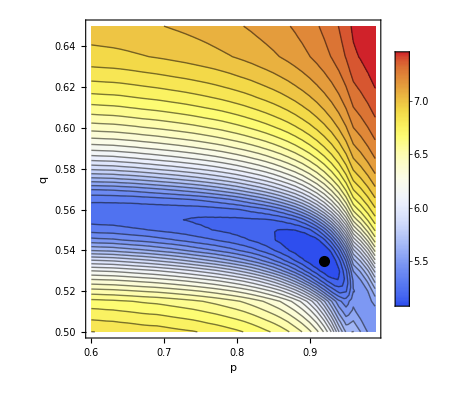

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"p","q"};
Clear[x,y,z];
lispoints=distListPythonTri/.{x_,y_,z_}->{x,y};
lisfilt=Flatten[MeanFilter[Partition[distListPythonTri,31]/.{x_,y_,z_}->Log[z],3]];
point=First[MinimalBy[Table[Append[lispoints[[i]],lisfilt[[i]]],{i,1,Length[lispoints]}],Last]/.{x_,y_,z_}->{x,y}];
gr1=ListContourPlot[Table[Append[lispoints[[i]],lisfilt[[i]]],{i,1,Length[lispoints]}],Contours->30,ColorFunction->ColorData["TemperatureMap"],Epilog->{PointSize[0.02],Point[point]},FrameLabel->frametext,PlotLegends->Automatic]
```

```mathematica
Export[prefix<>"erro2d.pdf",gr1]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/erro2d.pdf

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"p","q","  ℰ"};
gr1=ListPlot3D[Table[Append[lispoints[[i]],lisfilt[[i]]],{i,1,Length[lispoints]}],InterpolationOrder->3,ColorFunction->"Temperature",PlotRange->{{0.5,0.95},Automatic,Automatic},MeshFunctions->{#3&,#1&,#2&},Mesh->{30,10,10},MeshStyle->{None,Automatic,Automatic},MeshShading->{{Directive[{EdgeForm[],#}]&/@Table[ColorData["TemperatureMap"][shade],{shade,0,2,0.05}]}},AxesLabel->frametext,PlotLegends->Automatic]


Export[prefix<>"erro3d.pdf",Show[gr1]]
```

-Graphics3D-

/Users/neylemke/Luisa/BancodeDadosDoutorado/erro3d.pdf

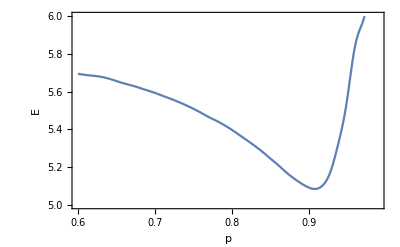

/Users/neylemke/Luisa/BancodeDadosDoutorado/erro1d.pdf

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"p"," E"};
gr1=ListPlot[Select[Table[Append[lispoints[[i]],lisfilt[[i]]],{i,1,Length[lispoints]}],#[[2]]==0.54&]/.{x_,y_,z_}->{x,z},Frame->True,FrameLabel->frametext,Joined->True,InterpolationOrder->5,PlotRange->{Automatic,{5,6}}]
Export[prefix<>"erro1d.pdf",Show[gr1]]
```

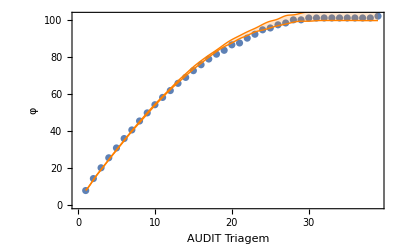

/Users/neylemke/Luisa/BancodeDadosDoutorado/varphipqqtri.pdf

```mathematica
lisvariassimul={};
lisvariassimul2={};
lisvariassimul3={};
lisvariassimul4={};
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
size0=Length[lisRTM];
size=Length[Join[liscontrole,lisintervencao]];
Do[
simul=(Nest[Step[p,q],#,150]& /@Table[0,{size0}]);
lisvariassimul=Append[lisvariassimul,simul];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Nest[Step[p,q],#,25]&/@simul2;
       simul4=Nest[Step[p,q],#,25]& /@simul3;
lisvariassimul2=Append[lisvariassimul2,simul2];
lisvariassimul3=Append[lisvariassimul3,simul3];
lisvariassimul4=Append[lisvariassimul3,simul4];
,
{10}]
lisdata=lisRTM;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisvariassimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
frametext=Style[#,"FontSize"->16]&/@{"AUDIT Triagem","φ"};
gr1=Show[{ListPlot[lisExp,Frame->True,FrameLabel->frametext],ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},InterpolationOrder->5]
}]
Export[prefix<>"varphipqqtri.pdf",Show[gr1]]
```

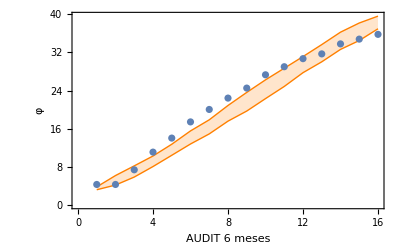

/Users/neylemke/Luisa/BancodeDadosDoutorado/varphipqqz6.pdf

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"AUDIT 6 meses","φ"};
lisdata=Join[liscontrolez6,lisintervencaoz6];
lisdatasimul=lisvariassimul3;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr1=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},Frame->True,FrameLabel->frametext],ListPlot[lisExp]
}]
Export[prefix<>"varphipqqz6.pdf",Show[gr1]]
```

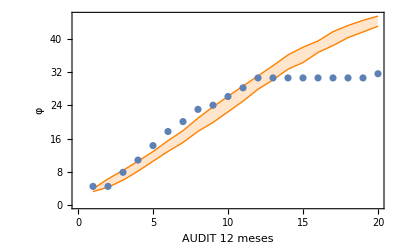

/Users/neylemke/Luisa/BancodeDadosDoutorado/varphipqqz12.pdf

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"AUDIT 12 meses","φ"};
lisdata=Join[liscontrolez12,lisintervencaoz12];
lisdatasimul=lisvariassimul4;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr1=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},Frame->True,FrameLabel->frametext],ListPlot[lisExp]
}]

Export[prefix<>"varphipqqz12.pdf",Show[gr1]]
```

```mathematica
Mean[Mean/@lisvariassimul3-Mean[Join[liscontrolez6,lisintervencaoz6]]]
Mean[Mean/@lisvariassimul4-Mean[Join[liscontrolez12,lisintervencaoz12]]]
```

5.15521

5.66951

```mathematica
scale=N[Floor[10*(HistogramList[lisRTM][[2,1]])/Length[lisRTM]]/10];
max=1.6;
listicksy=Table[{max*i/5,scale*i/5},{i,0,5}];
```

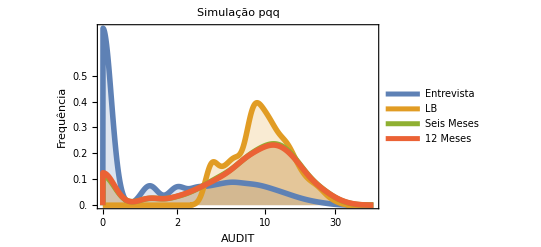

/Users/neylemke/Luisa/BancodeDadosDoutorado/expdistpqq.pdf

```mathematica
gr1=SmoothHistogram[{Log[Flatten[lisvariassimul]+1],Log[Flatten[lisvariassimul2]+1],Log[Flatten[lisvariassimul3]+1],Log[Flatten[lisvariassimul4]+1]},PlotLegends->LineLegend[{"Entrevista","LB", "Seis Meses","12 Meses"}],Axes->True,PlotRange->{{0,4},All},Filling->Bottom,PlotStyle->{Thickness[0.01]},Frame->True, FrameLabel->{Style["AUDIT",FontSize->18],Style["Frequência",FontSize->18]},FrameTicks->{listicksy,{{0,{Log[1+1],1},{Log[3],2},{Log[6],5},{Log[11],10},{Log[21],20},{Log[31],30},{Log[51],50}},None}},PlotLabel->Style["Simulação pqq", "FontSize"->16]]
Export[prefix<>"expdistpqq.pdf",gr1]
```

```mathematica
p
```

0.94

```mathematica
q
```

0.53

### Variação no r

```mathematica
size0=Length[lisRTM];
size=Length[Join[liscontrole,lisintervencao]];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N]
listDistr=ParallelTable[Print[r];Sum[
simul=Table[Steps[p,q,0,150],{size0}];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
(* Print[sizelocal,",",size,",",Length[simul2]]; *)
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
{r,compara[simul3,Join[liscontrolez6,lisintervencaoz6]]+compara[simul4,Join[liscontrolez12,lisintervencaoz12]]},{j,1,100}]/100,{r,0.50,0.75,0.005}];
```

{0.94,0.53,58.665}

0.5

0.525

0.55

0.575

0.58

0.555

0.53

0.505

0.585

0.56

0.535

0.51

0.59

0.565

0.54

0.515

0.595

0.57

0.545

0.52

0.6

0.615

0.635

0.655

0.605

0.62

0.64

0.66

0.61

0.625

0.645

0.665

0.675

0.63

0.65

0.67

0.68

0.695

0.715

0.735

0.685

0.7

0.72

0.74

0.69

0.705

0.725

0.745

0.71

0.73

0.75

```mathematica
distListPythonRisco=listDistr;
```

```mathematica
lisvariassimul={};
lisvariassimul2={};
lisvariassimul3={};
lisvariassimul4={};
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
r=First[First[MinimalBy[distListPythonRisco,Last]]];
Do[

simul=(Steps[p,q,#,150]& /@Table[0,{size0}]);
lisvariassimul=Append[lisvariassimul,simul];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
lisvariassimul2=Append[lisvariassimul2,simul2];
lisvariassimul3=Append[lisvariassimul3,simul3];
lisvariassimul4=Append[lisvariassimul4,simul4];
,
{10}]
```

```mathematica
First[First[MinimalBy[distListPythonRisco,Last]]]
```

0.62

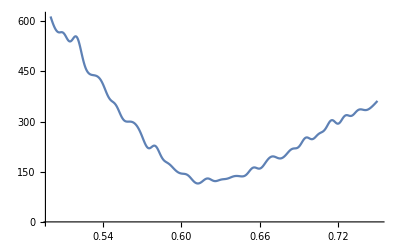

```mathematica
ListPlot[distListPythonRisco,Joined->True,InterpolationOrder->4]
```

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"AUDIT 6 meses","φ"};
lisdata=Join[liscontrolez6,lisintervencaoz6];
lisdatasimul=lisvariassimul3;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr1=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},Frame->True,FrameLabel->frametext],ListPlot[lisExp]
}]
Export[prefix<>"varphipqrz6.pdf",gr1]
```

-Graphics-

/Users/neylemke/Luisa/BancodeDadosDoutorado/varphipqrz6.pdf

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"AUDIT 12 meses","φ"};
lisdata=Join[liscontrolez12,lisintervencaoz12];
lisdatasimul=lisvariassimul4;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr1=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},Frame->True,FrameLabel->frametext],ListPlot[lisExp]
}]
Export[prefix<>"varphipqrz12.pdf",gr1]
```

-Graphics-

/Users/neylemke/Luisa/BancodeDadosDoutorado/varphipqrz12.pdf

```mathematica
Correlation[lisvariassimul4[[1]],lisvariassimul3[[1]]]//N
```

0.797665

```mathematica
Correlation[lisvariassimul2[[1]],lisvariassimul3[[1]]]//N
```

0.672024

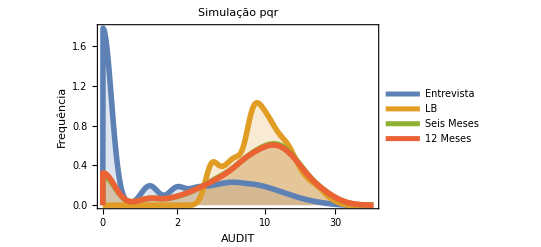

/Users/neylemke/Luisa/BancodeDadosDoutorado/expdistpqr.pdf

```mathematica
gr1=SmoothHistogram[{Log[Flatten[lisvariassimul]+1],Log[Flatten[lisvariassimul2]+1],Log[Flatten[lisvariassimul3]+1],Log[Flatten[lisvariassimul4]+1]},PlotLegends->LineLegend[{"Entrevista","LB", "Seis Meses","12 Meses"}],Axes->True,PlotRange->{{0,4},All},Filling->Bottom,PlotStyle->{Thickness[0.01]},Frame->True, FrameLabel->{Style["AUDIT",FontSize->18],Style["Frequência",FontSize->18]},FrameTicks->{{Automatic,None},{{0,{Log[1+1],1},{Log[3],2},{Log[6],5},{Log[11],10},{Log[21],20},{Log[31],30},{Log[51],50}},None}},PlotLabel->Style["Simulação pqr", "FontSize"->16]]
Export[prefix<>"expdistpqr.pdf",gr1]
```

### Grupos C e I

```mathematica
size0=Length[lisRTM];
size=Length[liscontrole];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N]

lisr1=Table[listDistr=ParallelTable[Print[r];Sum[
simul=Table[Steps[p,q,0,150],{size0}];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
(* Print[sizelocal,",",size,",",Length[simul2]]; *)
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
{r,compara[simul3,Join[liscontrolez6]]+compara[simul4,Join[liscontrolez12]]},{j,1,100}]/100,{r,0.55,0.7,0.005}];
First[First[MinimalBy[listDistr,Last]]],{10}];
```

{0.94,0.53,58.665}

0.55

0.57

0.59

0.61

0.615

0.595

0.555

0.575

0.62

0.6

0.56

0.58

0.625

0.605

0.565

0.585

0.63

0.65

0.67

0.69

0.635

0.675

0.655

0.695

0.64

0.68

0.66

0.7

0.645

0.685

0.665

0.55

0.57

0.59

0.61

0.615

0.595

0.575

0.555

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.695

0.675

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.595

0.615

0.575

0.555

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.695

0.675

0.64

0.66

0.7

0.68

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.575

0.555

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.66

0.64

0.7

0.68

0.665

0.645

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.575

0.555

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.7

0.68

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.575

0.555

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.575

0.555

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.575

0.555

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.575

0.555

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.575

0.555

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.695

0.675

0.64

0.66

0.7

0.68

0.645

0.665

0.685

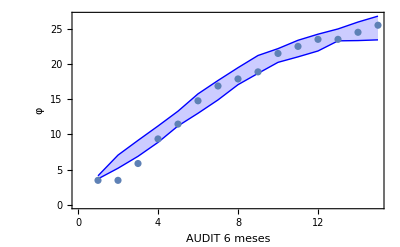

```mathematica
lisvariassimul={};
lisvariassimul2={};
lisvariassimul3={};
lisvariassimul4={};
lisdata=Join[liscontrolez6];
size=Length[lisdata];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
r=First[First[MinimalBy[listDistr,Last]]];
Do[
simul=(Steps[p,q,#,150]& /@Table[0,{size0}]);
lisvariassimul=Append[lisvariassimul,simul];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
lisvariassimul2=Append[lisvariassimul2,simul2];
lisvariassimul3=Append[lisvariassimul3,simul3];
lisvariassimul4=Append[lisvariassimul4,simul4];
,
{10}]

frametext=Style[#,"FontSize"->16]&/@{"AUDIT 6 meses","φ"};

lisdatasimul=lisvariassimul3;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr1=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Blue}},Frame->True,FrameLabel->frametext],ListPlot[lisExp]
}]
```

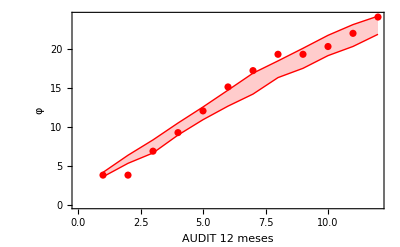

```mathematica
lisvariassimul={};
lisvariassimul2={};
lisvariassimul3={};
lisvariassimul4={};
lisdata=Join[liscontrolez12];
size=Length[lisdata];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
r=First[First[MinimalBy[listDistr,Last]]];
Do[

simul=(Steps[p,q,#,150]& /@Table[0,{size0}]);
lisvariassimul=Append[lisvariassimul,simul];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
lisvariassimul2=Append[lisvariassimul2,simul2];
lisvariassimul3=Append[lisvariassimul3,simul3];
lisvariassimul4=Append[lisvariassimul4,simul4];
,
{10}]

frametext=Style[#,"FontSize"->16]&/@{"AUDIT 12 meses","φ"};

lisdatasimul=lisvariassimul3;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr2=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Red}},Frame->True,FrameLabel->frametext],ListPlot[lisExp,PlotStyle->{{Thin,Red}}]
}]
```

```mathematica
size0=Length[lisRTM];
size=Length[lisintervencao];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N]
lisr2=Table[listDistr=ParallelTable[Print[r];Sum[
simul=Table[Steps[p,q,0,150],{size0}];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
(* Print[sizelocal,",",size,",",Length[simul2]]; *)
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
{r,compara[simul3,Join[lisintervencaoz6]]+compara[simul4,Join[lisintervencaoz12]]},{j,1,100}]/100,{r,0.55,0.7,0.005}];
First[First[MinimalBy[listDistr,Last]]]
,{10}]
```

{0.94,0.53,58.665}

0.55

0.57

0.59

0.61

0.615

0.595

0.575

0.555

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.7

0.68

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.575

0.555

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.7

0.68

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.555

0.575

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.555

0.575

0.62

0.6

0.58

0.56

0.625

0.605

0.565

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.575

0.555

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.575

0.555

0.62

0.6

0.56

0.58

0.625

0.605

0.565

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.555

0.575

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.555

0.575

0.62

0.6

0.56

0.58

0.625

0.605

0.565

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.555

0.575

0.62

0.6

0.56

0.58

0.625

0.605

0.565

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.575

0.555

0.62

0.6

0.58

0.56

0.625

0.605

0.585

0.565

0.63

0.65

0.67

0.69

0.635

0.655

0.695

0.675

0.64

0.66

0.7

0.68

0.645

0.665

0.685

{0.6,0.59,0.595,0.595,0.595,0.59,0.585,0.595,0.585,0.595}

0.63

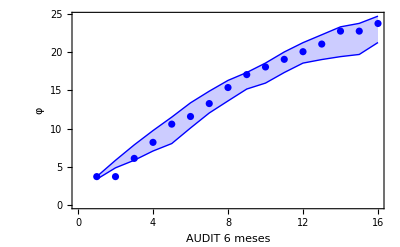

```mathematica
lisvariassimul={};
lisvariassimul2={};
lisvariassimul3={};
lisvariassimul4={};
lisdata=Join[lisintervencaoz6];
size=Length[lisdata];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
r=First[First[MinimalBy[listDistr,Last]]];
r=0.63
Do[

simul=(Steps[p,q,#,150]& /@Table[0,{size0}]);
lisvariassimul=Append[lisvariassimul,simul];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
lisvariassimul2=Append[lisvariassimul2,simul2];
lisvariassimul3=Append[lisvariassimul3,simul3];
lisvariassimul4=Append[lisvariassimul4,simul4];
,
{10}]

frametext=Style[#,"FontSize"->16]&/@{"AUDIT 6 meses","φ"};

lisdatasimul=lisvariassimul3;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr1=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Blue}},Frame->True,FrameLabel->frametext],ListPlot[lisExp,PlotStyle->{{Thin,Blue}}]
}]
```

```mathematica
r2=First[First[MinimalBy[listDistr,Last]]]
```

0.59

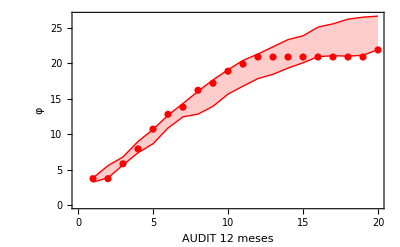

```mathematica
lisvariassimul={};
lisvariassimul2={};
lisvariassimul3={};
lisvariassimul4={};
lisdata=Join[lisintervencaoz12];
size=Length[lisdata];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
r=First[First[MinimalBy[listDistr,Last]]];
r=0.63;
Do[

simul=(Steps[p,q,#,150]& /@Table[0,{size0}]);
lisvariassimul=Append[lisvariassimul,simul];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
lisvariassimul2=Append[lisvariassimul2,simul2];
lisvariassimul3=Append[lisvariassimul3,simul3];
lisvariassimul4=Append[lisvariassimul4,simul4];
,
{10}]

frametext=Style[#,"FontSize"->16]&/@{"AUDIT 12 meses","φ"};

lisdatasimul=lisvariassimul3;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr2=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Red}},Frame->True,FrameLabel->frametext],ListPlot[lisExp,PlotStyle->{{Thin,Red}}]
}]
```

```mathematica
Export[prefix<>"comppqrCIB.pdf",Show[gr1,gr2]]
```

```mathematica
"/Users/neylemke/Luisa/BancodeDadosDoutorado/lis
```

Grupos

### AUDITESC

```mathematica
partGrupos=GroupBy[bbariscoz12,{#GRUPO,#SEXOS}&];
lisevol={"AUDITESC","z6AUDITESC","z12AUDITESC"}/.Normal[bbarisco1[All, {"AUDITESC","z6AUDITESC","z12AUDITESC"}]];
lisclus=ClusteringComponents[lisevol,3,1,Method->"Optimize"];
lisclus2=If[#==1,1,0]&/@lisclus;
labels={{"C","F"},{"C", "M"},{"I","F"},{"I","M"}};
```

-Graphics-

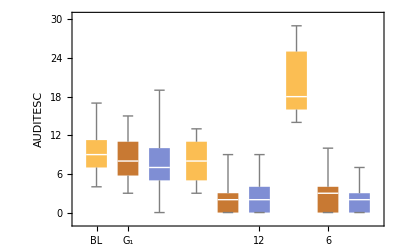

/Users/neylemke/Luisa/BancodeDadosDoutorado/perspie.pdf

/Users/neylemke/Luisa/BancodeDadosDoutorado/perscomp.pdf

/Users/neylemke/Luisa/BancodeDadosDoutorado/perspie.pdf

/Users/neylemke/Luisa/BancodeDadosDoutorado/perscomp.pdf

```mathematica
lisevol={"AUDITESC","z6AUDITESC","z12AUDITESC"}/.Normal[bbarisco1[All, {"AUDITESC","z6AUDITESC","z12AUDITESC"}]];
lisclus=ClusteringComponents[lisevol,3,1,Method->"Optimize"];
P3=
PieChart[Last/@Tally[lisclus],ChartStyle->8,ChartLabels->{Style["G_1",FontSize->24],Style["G_2",FontSize->24],Style["G_3",FontSize->24]} ]

gr3=BoxWhiskerChart[Table[Transpose[lisevol[[Flatten[Position[lisclus,k]]]]],{k,1,3}],ChartLabels->{{"\!\(\*SubscriptBox[\(G\), \(1\)]\)","\!\(\*SubscriptBox[\(G\), \(2\)]\)","\!\(\*SubscriptBox[\(G\), \(3\)]\)"},{"BL","6","12"}}, FrameLabel-> "AUDITESC"]
Export[prefix<>"perspie.pdf",P3 ]
Export[prefix<>"perscomp.pdf",gr3 ]
```

```mathematica
lisvarname={"SEXO", "RELIGI","INSTRCHE","RELIGIPR","PESO","ALTURA","RACA","IDADEBEB","AMBINGE","IDADE","FAMILAL","PERS"};
bglm=bestGeneralizedLinearModelFitDataset[bbapers2,lisvarname,"AIC",ExponentialFamily->"Binomial",NominalVariables->{sexo,religi,raca}];
bglm["BestFitParameters"]
bglm["ParameterPValues"]
bglm["ParameterConfidenceIntervals"]
bglm["ParameterTable"]
```

{1.43,-0.266907,-0.0645976,0.105452,0.127154}

{0.000239719,0.00646474,0.020439,0.0521798,0.168227}

{{0.666932,2.19307},{-0.459005,-0.0748084},{-0.119213,-0.00998216},{-0.000994764,0.211899},{-0.0537104,0.308018}}

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.43 | 0.389327 | 3.673 | 0.000239719
sexo | -0.266907 | 0.0980112 | -2.72323 | 0.00646474
idadebeb | -0.0645976 | 0.0278655 | -2.31819 | 0.020439
ambinge | 0.105452 | 0.0543107 | 1.94165 | 0.0521798
familal | 0.127154 | 0.0922793 | 1.37792 | 0.168227

```mathematica
varnames=assocvarnamesTex/@ToUpperCase/@(ToString/@bglm["ParameterTable"][[1,1,2;;-1,1]]);
tabparam={
bglm["BestFitParameters"],
bglm["ParameterConfidenceIntervals"],bglm["ParameterPValues"]};
tabparamTex=geraFitTabTex[tabparam,varnames];
Export[prefix<>"tabparam.tex",tabparamTex, "String"];
compilaTex[tabparamTex,prefix]
```

-Graphics-

```mathematica
bbapers=bbarisco1[Flatten[Position[lisclus,1]],lisvarname];
bbanpers=Union[bbarisco1[Flatten[Position[lisclus,2]],lisvarname],bbarisco1[Flatten[Position[lisclus,3]],lisvar]];
bbapers15=Dataset@MapThread[Append,{Normal[bbarisco1],Thread["PERS"->lisclus2]}];
catidades[num_]:=If[IntegerQ[num],If[num<12,0,If[num<14,1,2]],1]
liscatidade=catidades/@Normal@bbapers15[All,"IDADEBEB"];
bbapers2=Dataset@MapThread[Append,{Normal[bbapers15],Thread["CATIDADEBEB"->liscatidade]}];
```

```mathematica
lisvar={"SEXOS","AMBINGE","FAMILAL","CATIDADEBEB"};
partlsd=(GroupBy[bbapers2,#PERS&]);
tabci=geratablsd[partlsd,lisvar];
tabvarTex=geratabvarTex[tabci,"Vari\\'aveis",{"P","N"}, 2];
Export[prefix<>"tabvarpers.tex", tabvarTex,"String"]
compilaTex[tabvarTex,prefix]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabvarpers.tex

-Graphics-

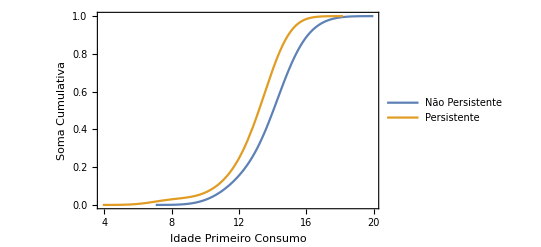

/Users/neylemke/Luisa/BancodeDadosDoutorado/cdfidade.pdf

```mathematica
sh=SmoothHistogram[Table[Cases[First/@({0,1}/.GroupBy[{"IDADEBEB","PERS"}/.Normal[bbapers2[All,{"IDADEBEB","PERS"}]],Last])[[i]],_Integer],{i,1,2}],1,"CDF",Frame->True,FrameLabel->{assocvarnames["IDADEBEB"],HoldForm["Soma Cumulativa"]},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]},PlotLegends->LineLegend[{"Não Persistente","Persistente"}]]

Export[prefix<>"cdfidade.pdf",sh ]
```

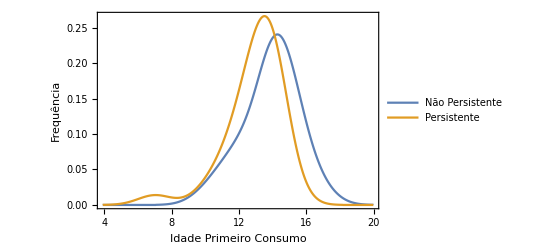

/Users/neylemke/Luisa/BancodeDadosDoutorado/pdfidade.pdf

```mathematica
sh=SmoothHistogram[Table[Cases[First/@ ({0,1}/.GroupBy[{"IDADEBEB","PERS"}/.Normal[bbapers2[All,{"IDADEBEB","PERS"}]],Last])[[i]],_Integer],{i,1,2}],1,"PDF",Frame->True,FrameLabel->{assocvarnames["IDADEBEB"],HoldForm["Frequência"]},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]},PlotLegends->LineLegend[{"Não Persistente","Persistente"}]]
Export[prefix<>"pdfidade.pdf",sh ]
```

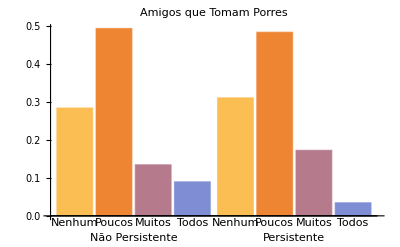

/Users/neylemke/Luisa/BancodeDadosDoutorado/ambinge.pdf

```mathematica
bc=BarChart[Table[N[Last/@Tally[First/@({0,1}/.Normal[GroupBy[{"AMBINGE","PERS"}/.Normal[bbapers2[All,{"AMBINGE","PERS"}]],Last]])⟦i⟧]/Length[({0,1}/.Normal[GroupBy[{"AMBINGE","PERS"}/.Normal[bbapers2[All,{"AMBINGE","PERS"}]],Last]])⟦i⟧]],{i,1,2}],ChartLabels->{{"Não Persistente","Persistente"},{"Nenhum","Poucos","Muitos","Todos"}},PlotLabel->assocvarnames["AMBINGE"],LabelStyle->{GrayLevel[0]}]
Export[prefix<>"ambinge.pdf",bc ]
```

```mathematica
pc=PieChart[Table[N[Last/@Tally[First/@({0,1}/.Normal[GroupBy[{"SEXO","PERS"}/.Normal[bbapers2[All,{"SEXO","PERS"}]],Last]])⟦i⟧]/Length[({0,1}/.Normal[GroupBy[{"SEXO","PERS"}/.Normal[bbapers2[All,{"SEXO","PERS"}]],Last]])⟦i⟧]],{i,1,2}],ChartLabels->{{"Não \n Persistente","Persistente"},{♂,♀,"3","4"}},PlotLabel->HoldForm["SEXO"],LabelStyle->{GrayLevel[0]}]

Export[prefix<>"sexo.pdf",pc ]
```

-Graphics-

/Users/neylemke/Luisa/BancodeDadosDoutorado/sexo.pdf

```mathematica
pc=PieChart[Table[N[Last/@Tally[First/@({0,1}/.Normal[GroupBy[{"FAMILAL","PERS"}/.Normal[bbapers2[All,{"FAMILAL","PERS"}]],Last]])⟦i⟧]/Length[({0,1}/.Normal[GroupBy[{"FAMILAL","PERS"}/.Normal[bbapers2[All,{"FAMILAL","PERS"}]],Last]])⟦i⟧]],{i,1,2}],ChartLabels->{{"Não \n Persistente","Persistente"},{"Não","Sim",3,4}},PlotLabel->assocvarnames["FAMILAL"],LabelStyle->{GrayLevel[0]}]
Export[prefix<>"familal.pdf",pc ]
```

-Graphics-

Sandbox

## Baixo Risco

```mathematica
gru1=Select[Normal@Select[bbabr,#RecusaIB12==0&][All,"AUDITESC"],IntegerQ];
gru2=Select[Normal@Select[bbabr,#RecusaIB12==0&][All,"z12AUDITESC"],IntegerQ];
LocationTest[{gru1,gru2}]
```

```mathematica
Mean[gru1]-Mean[gru2]//N
```

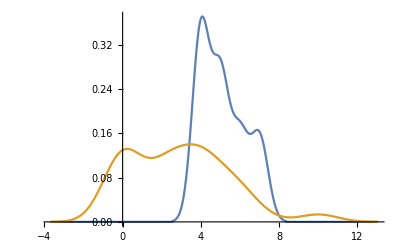

```mathematica
SmoothHistogram[{gru1,gru2}]
```

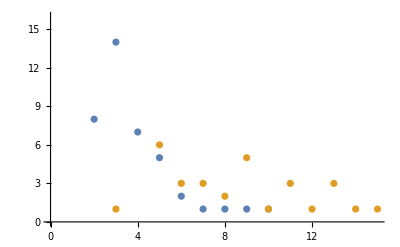

```mathematica
ListPlot[{Tally[Normal[Select[bbapers2,#PERS==0&][All,"z6AUDITESC"]]],
Tally[Normal[Select[bbapers2,#PERS==1&][All,"z6AUDITESC"]]]
}]
```

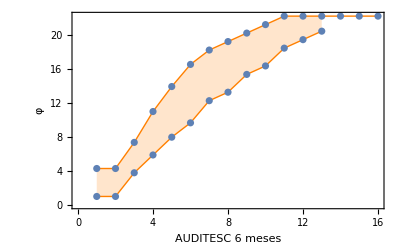

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"AUDITESC 6 meses","φ"};
lisdata=Normal[Select[bbapers2,#PERS==0&][All,"z6AUDITESC"]];
lisdata2=Normal[Select[bbapers2,#PERS==1&][All,"z6AUDITESC"]];
lisSumvarias=geraParcialSums[lisdata,Min[lisdata],Max[lisdata2]];
lisSumvarias2=geraParcialSums[lisdata2,Min[lisdata2],Max[lisdata2]];

gr1=Show[{ListPlot[{lisSumvarias,lisSumvarias2},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},Frame->True,FrameLabel->frametext],ListPlot[lisSumvarias],ListPlot[lisSumvarias2]
}]
Export[prefix<>"varphipqrz6.pdf",gr1]
```

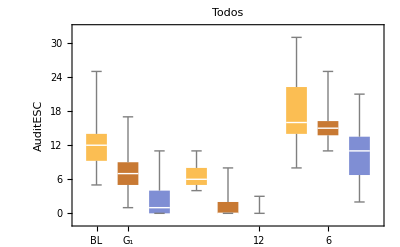

```mathematica
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
r=First[First[MinimalBy[distListPythonRisco,Last]]];

simul=Table[Steps[p,q,0,150],{size0}];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
lisevol=Transpose[{simul2,simul3,simul4}];
lisclus=ClusteringComponents[lisevol,3,1,Method->"Optimize"];

gr3=BoxWhiskerChart[Table[Transpose[lisevol[[Flatten[Position[lisclus,k]]]]],{k,1,3}],ChartLabels->{{"\!\(\*SubscriptBox[\(G\), \(1\)]\)","\!\(\*SubscriptBox[\(G\), \(2\)]\)","\!\(\*SubscriptBox[\(G\), \(3\)]\)"},{"BL","6","12"}},PlotLabel->"Todos", FrameLabel-> "AuditESC"]
```

```mathematica
Entropy[lisclus]//N
```

0.963789

```mathematica
lisSumvarias
```

{{3.94444,6.7362,8.83481,10.528,13.6074,16.6868,19.9894,22.5989,24.292,27.0838,29.8755},{4.3673,7.31321,9.6995,12.3089,12.3089,15.3884,18.1801,20.7896,23.399,25.7853,27.4785},{4.21888,6.60517,9.21461,12.1605,14.9523,18.0317,19.0317,21.6412,23.7398,26.6857,29.072},{4.68888,7.07517,9.46147,11.5601,13.9464,16.045,18.9909,21.6003,23.6989,26.6449,27.6449},{4.66356,6.76217,9.14847,11.7579,14.3673,17.1591,18.8523,21.4617,24.0711,25.0711,27.1697},{4.61092,6.99721,8.69036,11.4821,14.0916,16.701,17.701,19.3941,21.7804,24.5722,26.2653},{4.3673,7.44674,10.0562,11.7493,15.0519,17.8437,20.23,23.4272,24.4272,25.4272,27.1203},{4.29584,7.24175,8.93489,11.5443,14.1538,17.351,19.9604,21.6536,22.6536,24.7522,27.3616},{4.43399,6.5326,9.32436,12.4038,14.5024,16.601,19.7982,21.8969,24.6886,26.3818,28.7681},{4.3673,6.75359,8.8522,11.644,13.7426,16.352,19.2979,20.9911,23.3774,25.7637,28.8431}}

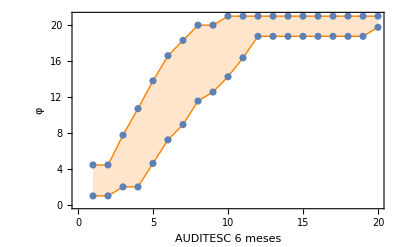

/Users/neylemke/Luisa/BancodeDadosDoutorado/varphipqrz6.pdf

lissimul2

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"AUDITESC 6 meses","φ"};
lisdata=Normal[Select[bbapers2,#PERS==0&][All,"z12AUDITESC"]];
lisdata2=Normal[Select[bbapers2,#PERS==1&][All,"z12AUDITESC"]];
lisSumvarias=geraParcialSums[lisdata,Min[lisdata],Max[lisdata2]];
lisSumvarias2=geraParcialSums[lisdata2,Min[lisdata2],Max[lisdata2]];

gr1=Show[{ListPlot[{lisSumvarias,lisSumvarias2},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},Frame->True,FrameLabel->frametext],ListPlot[lisSumvarias],ListPlot[lisSumvarias2]
}]
Export[prefix<>"varphipqrz6.pdf",gr1]
```

```mathematica
lisvarname={"SEXO", "INSTRCHE","IDADEBEB","AMBINGE","IDADE","FAMILAL","PERS"};
lisvar=ToExpression/@(ToLowerCase/@lisvarname);
datapoints=lisvarname/.Normal[bbapers2[All,lisvarname]];
datapoints=Cases[datapoints,Table[_Integer,Length[lisvarname]]];
```

```mathematica
datapointsml=Table[datapoints[[i,1;;-2]]->datapoints[[i,-1]],{i,1,Length[datapoints]}];
```

ClassifierFunction[…]

```mathematica
listeste=RandomChoice[liscases,Floor[Length[datapointsml]/2]];
listrain=Complement[liscases,listeste];
```

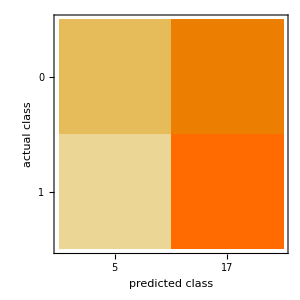

```mathematica
liscases=Table[i,{i,1,Length[datapointsml]}];
lispos=Select[datapointsml,#[[2]]==0&];
lisneg=Select[datapointsml,#[[2]]==1&];
listestepos=RandomChoice[lispos,11];
listesteneg=RandomChoice[lisneg,11];
listrainpos=Complement[lispos,listestepos][[1;;11]];
listrainneg=Complement[lisneg,listesteneg][[1;;11]];
listeste=Join[listestepos,listesteneg];
listrain=Join[listrainpos,listrainneg];
c=Classify[listeste,Method->"LogisticRegression"];
ClassifierMeasurements[c,listrain,"ConfusionMatrixPlot"]
```

```mathematica
?Classify
```

RowBox[{"Classify", "[", RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["example", "TI"], StyleBox["1", "TR"]], "→", SubscriptBox[StyleBox["class", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["example", "TI"], StyleBox["2", "TR"]], "→", SubscriptBox[StyleBox["class", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] generates a RowBox[{"ClassifierFunction", "[", StyleBox["…", "TR"], "]"}] based on the examples and classes given.
RowBox[{"Classify", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["example", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["example", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "→", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["class", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["class", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] also generates a RowBox[{"ClassifierFunction", "[", StyleBox["…", "TR"], "]"}] based on the examples and classes given.
RowBox[{"Classify", "[", RowBox[{"<|", RowBox[{RowBox[{SubscriptBox[StyleBox["class", "TI"], StyleBox["1", "TR"]], "→", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["example", "TI"], StyleBox["11", "TR"]], ",", SubscriptBox[StyleBox["example", "TI"], StyleBox["12", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], ",", RowBox[{SubscriptBox[StyleBox["class", "TI"], StyleBox["2", "TR"]], "→", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["example", "TI"], StyleBox["21", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], ",", StyleBox["…", "TR"]}], "|>"}], "]"}] generates a RowBox[{"ClassifierFunction", "[", StyleBox["…", "TR"], "]"}] based on an association of classes with their examples.
RowBox[{"Classify", "[", RowBox[{StyleBox["training", "TI"], ",", StyleBox["data", "TI"]}], "]"}] attempts to classify StyleBox["data", "TI"] using a classifier function deduced from the training set given.
RowBox[{"Classify", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"name\",\"TI\"]\)\"", ShowStringCharacters->True], ",", StyleBox["data", "TI"]}], "]"}] attempts to classify StyleBox["data", "TI"] using the built-in classifier function represented by "
StyleBox["name", "TI"]".
RowBox[{"Classify", "[", RowBox[{StyleBox["…", "TR"], ",", StyleBox["data", "TI"], ",", StyleBox["prop", "TI"]}], "]"}] gives the specified property of the classification associated with StyleBox["data", "TI"].

### AUDITC

-Graphics-

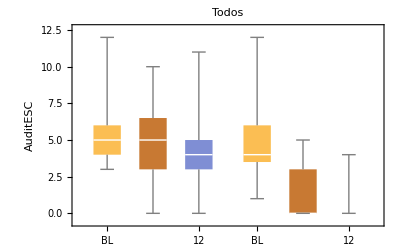

```mathematica
lisevol={"AUDITC","z6AUDITC","z12AUDITC"}/.Normal[bbarisco1[All, {"AUDITC","z6AUDITC","z12AUDITC"}]];
lisclus=ClusteringComponents[lisevol,2,1,Method->"Optimize"];
lisclus2=If[#==2,1,0]&/@lisclus;
P3=
PieChart[Last/@Tally[lisclus],ChartStyle->8,ChartLabels->{"G_1","G_2","G_3"}, PlotLabel->"Todos" ]

gr3=BoxWhiskerChart[Table[Transpose[lisevol[[Flatten[Position[lisclus,k]]]]],{k,1,2}],ChartLabels->{{"\!\(\*SubscriptBox[\(G\), \(1\)]\)","\!\(\*SubscriptBox[\(G\), \(2\)]\)","\!\(\*SubscriptBox[\(G\), \(3\)]\)"},{"BL","6","12"}},PlotLabel->"Todos", FrameLabel-> "AuditESC"]
```

```mathematica
bbapers2=Dataset@MapThread[Append,{Normal[bbarisco1],Thread["PERS"->lisclus2]}];
lisvarname={"SEXO", "RELIGI","INSTRCHE","RELIGIPR","PESO","RACA","IDADEBEB","AMBINGE","AMBEB","IDADE","FAMILAL","PERS"};
bglm=bestGeneralizedLinearModelFitDataset[bbapers2,lisvarname,"AIC",ExponentialFamily->"Binomial",NominalVariables->{sexo,religi,raca}];
bglm["BestFitParameters"]
bglm["ParameterPValues"]
bglm["ParameterConfidenceIntervals"]
bglm["ParameterTable"]
```

{2.8244,-0.0179754,0.0638082,-0.113983,-0.170603}

{0.0135702,0.00399878,0.0341123,0.0877089,0.125203}

{{0.581803,5.067},{-0.0302159,-0.00573498},{0.00478175,0.122835},{-0.244811,0.0168447},{-0.38868,0.0474738}}

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.8244 | 1.1442 | 2.46844 | 0.0135702
altura | -0.0179754 | 0.00624525 | -2.87826 | 0.00399878
idadebeb | 0.0638082 | 0.0301161 | 2.11874 | 0.0341123
ambinge | -0.113983 | 0.0667501 | -1.70761 | 0.0877089
familal | -0.170603 | 0.111266 | -1.53329 | 0.125203

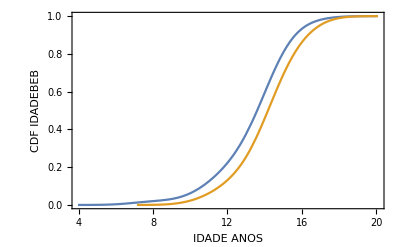

```mathematica
SmoothHistogram[Table[Cases[First/@ GroupBy[{"IDADEBEB","PERS"}/.Normal[bbapers2[All,{"IDADEBEB","PERS"}]],Last][[i]],_Integer],{i,1,2}],1,"CDF",Frame->True,FrameLabel->{HoldForm[IDADE ANOS],HoldForm[CDF IDADEBEB]},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Show[%1885,Frame->True,FrameLabel->{HoldForm[IDADE ANOS],HoldForm[CDF IDADEBEB]},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

-Graphics-

```mathematica
Clear[stepSelect]
```

```mathematica
data=Join[{"SEXO", "RELIGI","INSTRCHE","RELIGIPR","PESO","ALTURA",1}/.Normal[bbapers],{"SEXO", "RELIGI","INSTRCHE","RELIGIPR","PESO","ALTURA",0}/.Normal[bbanpers]];
glm=GeneralizedLinearModelFit[data,{sexo,religi,instrche,religipr,peso,altura},{sexo,religi,instrche,religipr,peso,altura}, NominalVariables->{sexo,religi},ExponentialFamily->"Binomial"];
glm["BestFitParameters"]
glm["ParameterPValues"]
glm["ParameterConfidenceIntervals"]
glm["ParameterTable"]
```

{-20.38,1.02053,15.7042,15.2401,15.537,0.177824,0.0366504,-0.0733484,0.00275701,0.0208192}

{0.993223,0.173446,0.994778,0.994932,0.994834,0.999958,0.916253,0.688233,0.890823,0.635999}

{{-4723.42,4682.66},{-0.448896,2.48996},{-4687.32,4718.73},{-4687.78,4718.26},{-4687.48,4718.56},{-6650.9,6651.25},{-0.646469,0.71977},{-0.431626,0.284929},{-0.0366101,0.0421242},{-0.0653943,0.107033}}

| Estimate | Standard Error | z-Statistic | P-Value
1 | -20.38 | 2399.56 | -0.00849325 | 0.993223
sexo[1] | 1.02053 | 0.749723 | 1.36121 | 0.173446
religi[0] | 15.7042 | 2399.54 | 0.00654467 | 0.994778
religi[1] | 15.2401 | 2399.54 | 0.00635126 | 0.994932
religi[2] | 15.537 | 2399.54 | 0.00647499 | 0.994834
religi[3] | 0.177824 | 3393.47 | 0.000052402 | 0.999958
instrche | 0.0366504 | 0.348537 | 0.105155 | 0.916253
religipr | -0.0733484 | 0.182798 | -0.401254 | 0.688233
peso | 0.00275701 | 0.0200857 | 0.137263 | 0.890823
altura | 0.0208192 | 0.0439873 | 0.473301 | 0.635999

{sexo,idadebeb,instrche,religipr}

Conclusão o modelo abaixo é o melhor!

```mathematica
lisvarnames={"SEXO","IDADEBEB"};
datalm=Join[Append[lisvarnames,1]/.Normal[bbapers],Append[lisvarnames,0]/.Normal[bbanpers]];
datalm=Cases[datalm,Table[_Integer,Length[lisvarnames]+1]];
lisvar=ToExpression/@(ToLowerCase/@lisvarnames);
glm=GeneralizedLinearModelFit[datalm,lisvar,lisvar,NominalVariables->{sexo}, ExponentialFamily->"Binomial"];
glm["BestFitParameters"]
glm["ParameterPValues"]
glm["ParameterConfidenceIntervals"]
glm["ParameterTable"]
glm["AIC"]
```

{2.7717,1.33131,-0.320163}

{0.176458,0.0122657,0.0343827}

{{-1.24714,6.79055},{0.289419,2.37321},{-0.616779,-0.0235467}}

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.7717 | 2.05047 | 1.35174 | 0.176458
sexo[1] | 1.33131 | 0.531589 | 2.50441 | 0.0122657
idadebeb | -0.320163 | 0.151338 | -2.11555 | 0.0343827

91.8781

```mathematica
data=Join[{"SEXO","IDADEBEB",0,"AUDITESC"}/.Normal[bbarisco1],{"SEXO","IDADEBEB",6,"z6AUDITESC"}/.Normal[bbarisco1],{"SEXO","IDADEBEB",12,"z12AUDITESC"}/.Normal[bbarisco1]];
data=Cases[data,{_Integer,_Integer,_Integer,_Integer}];
```

```mathematica
glm=GeneralizedLinearModelFit[data,{sexo,idadebeb,time},{sexo,idadebeb,time}, NominalVariables->{sexo},ExponentialFamily->"Poisson"];
glm["BestFitParameters"]
glm["ParameterPValues"]
glm["ParameterConfidenceIntervals"]
glm["ParameterTable"]
```

{3.13473,0.0574325,-0.0669389,-0.102871}

{3.67329×10^-54,0.289718,4.30059×10^-6,4.02214×10^-68}

{{2.73825,3.53121},{-0.0488878,0.163753},{-0.0954831,-0.0383947},{-0.114431,-0.0913108}}

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.13473 | 0.202289 | 15.4963 | 3.67329×10^-54
sexo[1] | 0.0574325 | 0.054246 | 1.05874 | 0.289718
idadebeb | -0.0669389 | 0.0145636 | -4.5963 | 4.30059×10^-6
time | -0.102871 | 0.0058982 | -17.4411 | 4.02214×10^-68

```mathematica
lisevol={"AUDITESC","z6AUDITESC","z12AUDITESC"}/.Normal[bbarisco1[All, {"AUDITESC","z6AUDITESC","z12AUDITESC"}]];
liscoeff=Table[lm=LinearModelFit[Log[lisevol[[i]]+1],x,x];
lm["BestFitParameters"][[2]],{i,1,Length[lisevol]}];
lisdata={"SEXO","INSTRCHE","IDADEBEB"}/.Normal[bbarisco1[All,{"SEXO","INSTRCHE","IDADEBEB"}]];
lisdatacomp=Flatten/@(Transpose@{lisdata,liscoeff});
lisdatacomp=Cases[lisdatacomp,{_Integer,_Integer,_Integer,_}];
lm=LinearModelFit[lisdatacomp,{sexo,instrche,idadebeb},{sexo,instrche,idadebeb}, NominalVariables->{sexo},IncludeConstantBasis->True];
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.511438 | 0.518359 | 0.986648 | 0.326827
sexo[1] | 0.351475 | 0.118068 | 2.9769 | 0.00386398
instrche | -0.107338 | 0.0681412 | -1.57523 | 0.1192
idadebeb | -0.0713668 | 0.0326715 | -2.18437 | 0.0319002

```mathematica
lisevol={"AUDITESC","z6AUDITESC","z12AUDITESC"}/.Normal[bbarisco1[All, {"AUDITESC","z6AUDITESC","z12AUDITESC"}]];
liscoeff=Table[lm=LinearModelFit[Log[lisevol[[i]]+1],x,x];
lm["BestFitParameters"][[1]],{i,1,Length[lisevol]}];
lisdata={"SEXO","INSTRCHE","IDADEBEB","GRUPO"}/.Normal[bbarisco1[All,{"SEXO","INSTRCHE","IDADEBEB","GRUPO"}]];
lisdatacomp=Flatten/@(Transpose@{lisdata,liscoeff});
lisdatacomp=Cases[lisdatacomp,{_Integer,_Integer,_Integer,_,_}];
lm=LinearModelFit[lisdatacomp,{sexo,instrche,idadebeb,grupo},{sexo,instrche,idadebeb,grupo}, NominalVariables->{sexo}];
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.17798 | 0.882597 | 2.46769 | 0.0157887
sexo[1] | -0.421047 | 0.198772 | -2.11824 | 0.0373387
instrche | 0.0822157 | 0.11472 | 0.716665 | 0.475721
idadebeb | 0.0455838 | 0.0550317 | 0.82832 | 0.410017
grupo[C] | -0.150003 | 0.184591 | -0.812622 | 0.418908

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.461316 | 0.526347 | 0.876449 | 0.383478
sexo[1] | 0.352891 | 0.11854 | 2.97698 | 0.0038762
instrche | -0.106497 | 0.0684145 | -1.55665 | 0.123603
idadebeb | -0.0706014 | 0.0328188 | -2.15125 | 0.0345516
grupo[C] | 0.0695843 | 0.110083 | 0.632107 | 0.529166

```mathematica
REvaluate["
  {
library(nlme)

ctrl <- lmeControl(opt='optim')

bba.lme.1<-lme(value ~variable*GRUPO*SEXOS, random = ~ variable |ID,data=gdf.m,control=ctrl,na.action=na.exclude)
summary(bba.lme.1)}"]
```

REvaluate::rerr: Failed to retrieve the value for variable or piece of code 
  {
library(nlme)

ctrl <- lmeControl(opt='optim')

bba.lme.1<-lme(value ~variable*GRUPO*SEXOS, random = ~ variable |ID,data=gdf.m,control=ctrl,na.action=na.exclude)
summary(bba.lme.1)}. The following R error was encountered: Error in is.data.frame(data) : object 'gdf.m' not found

$Failed

```mathematica
fsex/@data[[All,1]]//Tally
```

{{F,51},{M,31}}

```mathematica
data=Join[{"SEXO","INSTRCHE","IDADEBEB",1}/.Normal[bbapers],{"SEXO", "INSTRCHE","IDADEBEB",0}/.Normal[bbanpers]];
data=Delete[data,-14];

data=data/.{a_,b_,c_,d_,x_}:>{a,b,c,fclasse[d],x};
glm=GeneralizedLinearModelFit[data,{sexo,instrche,idadebeb},{sexo,instrche,idadebeb}, NominalVariables->{sexo},ExponentialFamily->"Binomial"];
glm["BestFitParameters"]
glm["ParameterPValues"]
glm["ParameterConfidenceIntervals"]
glm["ParameterTable"]
```

GeneralizedLinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

GeneralizedLinearModelFit[{{2,2,13,1},{1,4,14,1},{1,3,12,1},{2,4,13,1},{1,3,14,1},{1,2,13,1},{1,3,14,1},{2,3,14,1},{2,2,14,1},{1,3,10,1},{2,3,14,1},{1,2,14,1},{1,4,11,1},{2,2,12,1},{1,4,15,1},{1,4,12,1},{1,4,13,1},{2,3,14,1},{2,2,7,1},{1,1,17,1},{2,1,11,1},{1,3,13,1},{1,2,14,1},{1,3,12,0},{1,4,13,0},{1,2,15,0},{1,3,15,0},{1,3,14,0},{1,3,11,0},{1,3,14,0},{1,3,14,0},{1,3,15,0},{1,3,12,0},{1,4,10,0},{1,4,14,0},{1,1,16,0},{1,2,15,0},{1,3,15,0},{1,3,15,0},{1,3,11,0},{2,1,14,0},{2,2,14,0},{2,2,12,0},{2,2,15,0},{2,2,14,0},{2,3,11,0},{2,1,15,0},{2,1,15,0},{2,1,14,0},{2,2,14,0},{2,2,14,0},{2,2,15,0},{2,2,13,0},{2,2,17,0},{2,2,14,0},{2,2,14,0},{2,2,14,0},{2,2,13,0},{2,3,14,0},{2,3,16,0},{2,3,,0},{2,3,15,0},{2,3,15,0},{2,3,13,0},{2,3,14,0},{2,3,14,0},{2,3,15,0},{2,3,11,0},{2,3,14,0},{2,3,17,0},{2,3,14,0},{2,3,14,0},{2,4,15,0},{2,4,13,0},{2,4,14,0},{2,4,10,0},{2,2,15,0},{2,2,12,0},{2,2,15,0},{2,3,16,0},{2,3,16,0},{2,1,16,0},{2,2,14,0}},{sexo,instrche,idadebeb},{sexo,instrche,idadebeb},NominalVariables→{sexo},ExponentialFamily→Binomial][BestFitParameters]

GeneralizedLinearModelFit[{{2,2,13,1},{1,4,14,1},{1,3,12,1},{2,4,13,1},{1,3,14,1},{1,2,13,1},{1,3,14,1},{2,3,14,1},{2,2,14,1},{1,3,10,1},{2,3,14,1},{1,2,14,1},{1,4,11,1},{2,2,12,1},{1,4,15,1},{1,4,12,1},{1,4,13,1},{2,3,14,1},{2,2,7,1},{1,1,17,1},{2,1,11,1},{1,3,13,1},{1,2,14,1},{1,3,12,0},{1,4,13,0},{1,2,15,0},{1,3,15,0},{1,3,14,0},{1,3,11,0},{1,3,14,0},{1,3,14,0},{1,3,15,0},{1,3,12,0},{1,4,10,0},{1,4,14,0},{1,1,16,0},{1,2,15,0},{1,3,15,0},{1,3,15,0},{1,3,11,0},{2,1,14,0},{2,2,14,0},{2,2,12,0},{2,2,15,0},{2,2,14,0},{2,3,11,0},{2,1,15,0},{2,1,15,0},{2,1,14,0},{2,2,14,0},{2,2,14,0},{2,2,15,0},{2,2,13,0},{2,2,17,0},{2,2,14,0},{2,2,14,0},{2,2,14,0},{2,2,13,0},{2,3,14,0},{2,3,16,0},{2,3,,0},{2,3,15,0},{2,3,15,0},{2,3,13,0},{2,3,14,0},{2,3,14,0},{2,3,15,0},{2,3,11,0},{2,3,14,0},{2,3,17,0},{2,3,14,0},{2,3,14,0},{2,4,15,0},{2,4,13,0},{2,4,14,0},{2,4,10,0},{2,2,15,0},{2,2,12,0},{2,2,15,0},{2,3,16,0},{2,3,16,0},{2,1,16,0},{2,2,14,0}},{sexo,instrche,idadebeb},{sexo,instrche,idadebeb},NominalVariables→{sexo},ExponentialFamily→Binomial][ParameterPValues]

GeneralizedLinearModelFit[{{2,2,13,1},{1,4,14,1},{1,3,12,1},{2,4,13,1},{1,3,14,1},{1,2,13,1},{1,3,14,1},{2,3,14,1},{2,2,14,1},{1,3,10,1},{2,3,14,1},{1,2,14,1},{1,4,11,1},{2,2,12,1},{1,4,15,1},{1,4,12,1},{1,4,13,1},{2,3,14,1},{2,2,7,1},{1,1,17,1},{2,1,11,1},{1,3,13,1},{1,2,14,1},{1,3,12,0},{1,4,13,0},{1,2,15,0},{1,3,15,0},{1,3,14,0},{1,3,11,0},{1,3,14,0},{1,3,14,0},{1,3,15,0},{1,3,12,0},{1,4,10,0},{1,4,14,0},{1,1,16,0},{1,2,15,0},{1,3,15,0},{1,3,15,0},{1,3,11,0},{2,1,14,0},{2,2,14,0},{2,2,12,0},{2,2,15,0},{2,2,14,0},{2,3,11,0},{2,1,15,0},{2,1,15,0},{2,1,14,0},{2,2,14,0},{2,2,14,0},{2,2,15,0},{2,2,13,0},{2,2,17,0},{2,2,14,0},{2,2,14,0},{2,2,14,0},{2,2,13,0},{2,3,14,0},{2,3,16,0},{2,3,,0},{2,3,15,0},{2,3,15,0},{2,3,13,0},{2,3,14,0},{2,3,14,0},{2,3,15,0},{2,3,11,0},{2,3,14,0},{2,3,17,0},{2,3,14,0},{2,3,14,0},{2,4,15,0},{2,4,13,0},{2,4,14,0},{2,4,10,0},{2,2,15,0},{2,2,12,0},{2,2,15,0},{2,3,16,0},{2,3,16,0},{2,1,16,0},{2,2,14,0}},{sexo,instrche,idadebeb},{sexo,instrche,idadebeb},NominalVariables→{sexo},ExponentialFamily→Binomial][ParameterConfidenceIntervals]

GeneralizedLinearModelFit[{{2,2,13,1},{1,4,14,1},{1,3,12,1},{2,4,13,1},{1,3,14,1},{1,2,13,1},{1,3,14,1},{2,3,14,1},{2,2,14,1},{1,3,10,1},{2,3,14,1},{1,2,14,1},{1,4,11,1},{2,2,12,1},{1,4,15,1},{1,4,12,1},{1,4,13,1},{2,3,14,1},{2,2,7,1},{1,1,17,1},{2,1,11,1},{1,3,13,1},{1,2,14,1},{1,3,12,0},{1,4,13,0},{1,2,15,0},{1,3,15,0},{1,3,14,0},{1,3,11,0},{1,3,14,0},{1,3,14,0},{1,3,15,0},{1,3,12,0},{1,4,10,0},{1,4,14,0},{1,1,16,0},{1,2,15,0},{1,3,15,0},{1,3,15,0},{1,3,11,0},{2,1,14,0},{2,2,14,0},{2,2,12,0},{2,2,15,0},{2,2,14,0},{2,3,11,0},{2,1,15,0},{2,1,15,0},{2,1,14,0},{2,2,14,0},{2,2,14,0},{2,2,15,0},{2,2,13,0},{2,2,17,0},{2,2,14,0},{2,2,14,0},{2,2,14,0},{2,2,13,0},{2,3,14,0},{2,3,16,0},{2,3,,0},{2,3,15,0},{2,3,15,0},{2,3,13,0},{2,3,14,0},{2,3,14,0},{2,3,15,0},{2,3,11,0},{2,3,14,0},{2,3,17,0},{2,3,14,0},{2,3,14,0},{2,4,15,0},{2,4,13,0},{2,4,14,0},{2,4,10,0},{2,2,15,0},{2,2,12,0},{2,2,15,0},{2,3,16,0},{2,3,16,0},{2,1,16,0},{2,2,14,0}},{sexo,instrche,idadebeb},{sexo,instrche,idadebeb},NominalVariables→{sexo},ExponentialFamily→Binomial][ParameterTable]

-Graphics-

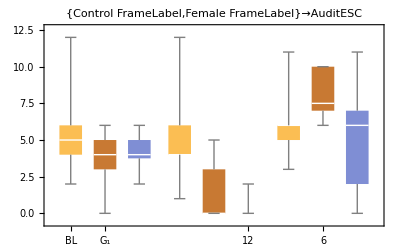

```mathematica
l=1;
lisevol={"AUDITC"*1.,"z6AUDITC","z12AUDITC"}/.Normal[bbarisco1[All, {"AUDITC","z6AUDITC","z12AUDITC"}]];
lisclus=ClusteringComponents[lisevol,3,1,Method->"KMeans"];
P3=
PieChart[Tally[lisclus]/.{x_,y_}->y,ChartStyle->8,ChartLabels->{"G_1","G_2","G_3"}, PlotLabel->StringReplace[labels[[l]],{"C"->"Control","I"->"Intervention","M"->"Male","F"->"Female"}] ]

gr3=BoxWhiskerChart[Table[Transpose[lisevol[[Flatten[Position[lisclus,k]]]]],{k,1,ngrupos[[l]]}],ChartLabels->{{"\!\(\*SubscriptBox[\(G\), \(1\)]\)","\!\(\*SubscriptBox[\(G\), \(2\)]\)","\!\(\*SubscriptBox[\(G\), \(3\)]\)"},{"BL","6","12"}},PlotLabel->StringReplace[labels[[l]],{"C"->"Control","I"->"Intervention","M"->"Male","F"->"Female"}]FrameLabel-> "AuditESC"]

lisvar={"SEXO", "RELIGI","CLASSE","INSTRCHE","RELIGIPR","PESO","ALTURA","RACA","IDADEBEB","AMIGBEB","AMBINGE","IDADE","FAMILAL","CLASSE"};
bbapers=bbarisco1[Flatten[Position[lisclus,3]],lisvar];
bbanpers=Union[bbarisco1[Flatten[Position[lisclus,2]],lisvar],bbarisco1[Flatten[Position[lisclus,1]],lisvar]];
```

```mathematica
data=Join[{"SEXO","INSTRCHE","IDADEBEB",1}/.Normal[bbapers],{"SEXO", "INSTRCHE","IDADEBEB",0}/.Normal[bbanpers]];
data=Delete[data,-14];
data=Delete[data,-24];
data=data/.{a_,b_,c_,d_,x_}:>{a,b,c,fclasse[d],x};
glm=GeneralizedLinearModelFit[data,{sexo,instrche,idadebeb},{sexo,instrche,idadebeb}, NominalVariables->{sexo},ExponentialFamily->"Binomial"];
glm["BestFitParameters"]
glm["ParameterPValues"]
glm["ParameterConfidenceIntervals"]
glm["ParameterTable"]
```

{0.157063,0.120711,0.137544,-0.159708}

{0.951656,0.849595,0.714254,0.331771}

{{-4.92053,5.23466},{-1.12688,1.3683},{-0.598718,0.873807},{-0.482226,0.16281}}

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.157063 | 2.59066 | 0.0606268 | 0.951656
sexo[1] | 0.120711 | 0.636539 | 0.189636 | 0.849595
instrche | 0.137544 | 0.375651 | 0.366149 | 0.714254
idadebeb | -0.159708 | 0.164553 | -0.970554 | 0.331771

```mathematica
data[[-24,-2]]
```

```mathematica
lisevol=Transpose[{partauditc1[[4]],partauditc1z6[[4]],partauditc1z12[[4]]}];
lisclus=ClusteringComponents[lisevol,2,1,Method->"KMeans"];
lisevol2=Table[N[Mean/@ Transpose[lisevol[[Flatten[Position[lisclus,k]]]]]],{k,1,2}];

P4=PieChart[Tally[lisclus]/.{x_,y_}->y,ChartStyle->8,ChartLabels->Reverse[{"\!\(\*SubscriptBox[\(G\), \(2\)]\)","\!\(\*SubscriptBox[\(G\), \(1\)]\)"}],PlotLabel->StringReplace[labels[[4]],{"C"->"Control","I"->"Intervention","M"->"Male","F"->"Female"}]];

gr4=BoxWhiskerChart[Reverse[Table[Transpose[lisevol[[Flatten[Position[lisclus,k]]]]],{k,1,2}]],ChartLabels->{{"G_1","G_2"},{"BL","6","12"}},FrameLabel-> "AuditC", PlotLabel->StringReplace[labels[[4]],{"C"->"Control","I"->"Intervention","M"->"Male","F"->"Female"}]];
```

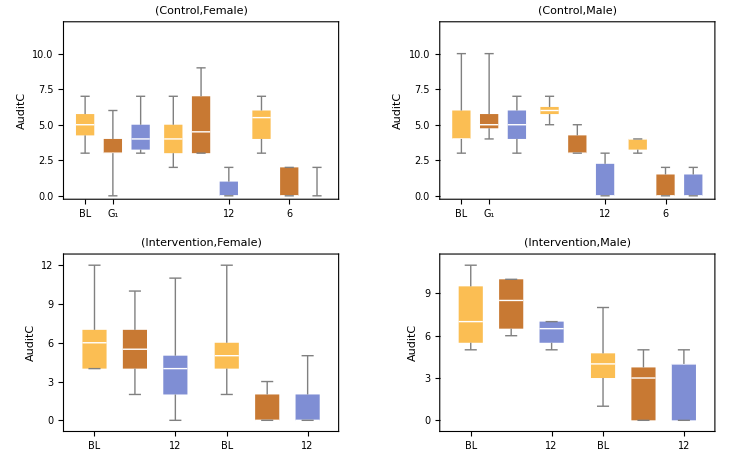

```mathematica
gg1=GraphicsGrid[{{gr1,gr2},{gr3,gr4}}]
```

```mathematica
Export["/Users/neylemke/Luisa/BancodeDadosDoutorado/chartsgrupos.pdf",gg1]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/chartsgrupos.pdf

```mathematica
gg2=GraphicsGrid[{{P1,P2},{P3,P4}}]
```

-Graphics-

```mathematica
Export["/Users/neylemke/Luisa/BancodeDadosDoutorado/piechartsgrupos.pdf",gg2]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/piechartsgrupos.pdf

{4.90909,3.27273,4.27273}

```mathematica
liskkk=Table[
lisevol[[Flatten[Position[lisclus,k]]] ],{k,1,2}]
```

{{{3,0,5},{4,4,5},{4,5,4},{5,5,4},{3,3,3},{3,0,0},{5,3,4},{8,3,4},{2,0,0},{1,3,0},{4,0,0}},{{5,7,7},{11,6,7},{6,10,6},{8,10,5}}}

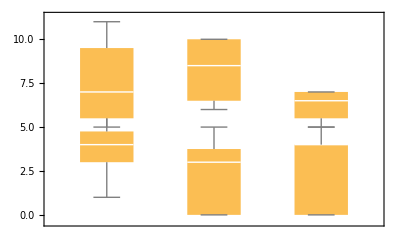

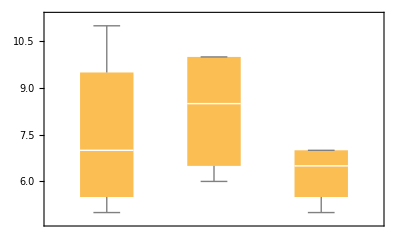

```mathematica
gr1=BoxWhiskerChart[liskkk[[1]]//Transpose];
gr2=BoxWhiskerChart[liskkk[[2]]//Transpose];
Show[gr1,gr2]
```

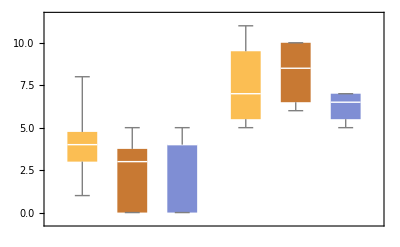

```mathematica
BoxWhiskerChart[{liskkk[[1]]//Transpose,liskkk[[2]]//Transpose}]
```

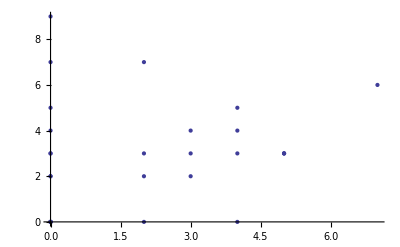

```mathematica
ListPlot[Transpose[{partauditc1z12[[1]],partauditc1z6[[1]]}]]
```

```mathematica
partauditc1[[2,-4]]=3;
Table[lm=LinearModelFit[Transpose[{partauditc1[[j]],partauditc1z6[[j]]}],x,x];
(lm["BestFitParameters"])[[2]],{j,1,4}]
```

{0.141533,0.525485,0.01,0.739407}

```mathematica
partauditc1[[2,-4]]=3;
Table[lm=LinearModelFit[Transpose[{partauditc1z12[[j]],partauditc1z6[[j]]}],x,x];
(lm["BestFitParameters"])[[2]],{j,1,4}]
```

{0.22564,0.782609,0.572822,0.931507}

```mathematica
partauditc1[[2,-4]]=3;
Table[lm=LinearModelFit[Transpose[{partauditc1z12[[j]],partauditc1[[j]]}],x,x];
(lm["BestFitParameters"])[[2]],{j,1,4}]
```

{0.080294,0.0652174,0.0833518,0.694064}

```mathematica
labels
```

{(C,F),(C,M),(I,M),(I,F)}

```mathematica
Prepend[Table[{labels[[i]],{SignedRankTest[{partauditc1[[i]],partauditc1z6[[i]]}],SignedRankTest[{partauditc1[[i]],partauditc1z12[[i]]}],SignedRankTest[{partauditc1z6[[i]],partauditc1z12[[i]]}]}},{i,1,4}],{"Grupo",{".1dLB-6","LB-12","6-12"}}]//Grid
```

Grupo | {.1dLB-6,LB-12,6-12}
(C,F) | {0.00220239,0.0000266405,0.128089}
(C,M) | {0.105978,0.011412,0.0136217}
(I,M) | {0.00168005,0.000378463,0.49192}
(I,F) | {0.205371,0.0578773,0.714815}

```mathematica
labels
```

{(C,F),(C,M),(I,M),(I,F)}

```mathematica
μ=Mean[Select[data1[[All,col["AUDIT1"]]],NumberQ]]+Mean[Select[data1[[All,col["AUDIT2"]]],NumberQ]]+Mean[Select[data1[[All,col["AUDIT3"]]],NumberQ]]//N;partauditc1[[2,-4]]=3;
Table[lm=LinearModelFit[Transpose[{partauditc1[[j]]-μ,partauditc1z6[[j]]-μ}],x,x];
{lm["BestFitParameters"][[1]],lm["ParameterConfidenceIntervals"][[1]],lm["ParameterPValues"][[1]]},{j,1,4}]
```

{{0.996031,{-1.43325,3.42531},0.407585},{0.794442,{-2.18965,3.77853},0.578805},{1.22912,{-1.44785,3.90608},0.351337},{0.0206969,{-2.63058,2.67197},0.986801}}

```mathematica
partauditc1[[2,-4]]=3;
Table[lm=LinearModelFit[Transpose[{partauditc1[[j]],partauditc1z6[[j]]}],x,x];
(lm["BestFitParameters"]),{j,1,4}]
```

{{2.19345,0.141533},{1.45631,0.525485},{2.61,0.01},{0.384181,0.739407}}

```mathematica
"SOLV12","COCA12","CRACK12","MACON12","ANFETA12","LSD12","ANTICOLI","ANABOLI1","EXT12","TRANQ12","TABC12","TABCDIA1","OTRDRG12"
```